```mathematica
Clear["Global`*"]

(* 
  IMPORTANT THINGS TO CHANGE BEFORE RUNNING THIS PROGRAM!!! 
MAKE SURE TO CHANGE THE FILE PATHS FOR THE b->sγ CONSTRAINT
AND THE DWARF SPHEROIDAL GALAXY CONSTRAINT TO WHERE YOU HAVE 
SAVED THE FILES. THE FILES ARE CURRENTLY LOCATED IN THE 
DROPBOX BUT THE PATH LEADS TO THEIR PATH OF MY LOCAL SAVES.
FURTHERMORE, YOU SHOULD CHANGE THE PATH OF  THE RESULTING FILE. 
FINALLY, CHANGE WHETHER YOU WANT TO USE THE TIGHT OR LOOSE b->sγ 
CONSTRAINT AND HOW MANY POINTS YOU WANT TO GENERATE. YOU CAN 
CHANGE THEM IN THE FOLLOWING VARIABLES.
 *)

relicFilePath="C:\\Users\\AlexandrePoulin\\Documents\\relic\\freezeout_v2.2\\outputFiles\\outputOmega.txt";

looseFilePath="C:\\Users\\AlexandrePoulin\\Documents\\GMSingletNotes\\mathematica stuff\\bsgloose.data";
tightFilePath= "C:\\Users\\AlexandrePoulin\\Documents\\GMSingletNotes\\mathematica stuff\\bsgtight.data";

dSphbb = "C:\\Users\\AlexandrePoulin\\Documents\\GMSingletNotes\\mathematica stuff\\lat_dsphs_p8_6yr_limits_bb.txt";
dSphee = "C:\\Users\\AlexandrePoulin\\Documents\\GMSingletNotes\\mathematica stuff\\lat_dsphs_p8_6yr_limits_ee.txt";
dSphmumu = "C:\\Users\\AlexandrePoulin\\Documents\\GMSingletNotes\\mathematica stuff\\lat_dsphs_p8_6yr_limits_mumu.txt";
dSphtautau = "C:\\Users\\AlexandrePoulin\\Documents\\GMSingletNotes\\mathematica stuff\\lat_dsphs_p8_6yr_limits_tautau.txt";
dSphuu = "C:\\Users\\AlexandrePoulin\\Documents\\GMSingletNotes\\mathematica stuff\\lat_dsphs_p8_6yr_limits_uu.txt";
dSphww = "C:\\Users\\AlexandrePoulin\\Documents\\GMSingletNotes\\mathematica stuff\\lat_dsphs_p8_6yr_limits_ww.txt";

luxPath = "C:\\Users\\AlexandrePoulin\\Documents\\GMSingletNotes\\mathematica stuff\\luxData.txt";
xenon10Path = "C:\\Users\\AlexandrePoulin\\Documents\\GMSingletNotes\\mathematica stuff\\xenon10Data.txt";


exportedFileName="C:\\Users\\AlexandrePoulin\\Documents\\GMSingletNotes\\mathematica stuff\\data_1000_Res_NoCon_v13.mx";
mathematicaOut ="C:\\Users\\AlexandrePoulin\\Documents\\relic\\freezeout_v2.2\\inputFiles\\mathematicaOut.txt";

tight=False; (*use tight b->s+γ constraint, False uses loose*)
numberOfPoints=1000; (*number of points generated*)
useBSG = False; (* whether or not to use b->sγ *)
useDD = False; (* whether or not to use direct detection *)
useDSPH = False; (* whether or not to use dSph constraint *)
useInv = False; (* whether or not to use invisible decay constraint *)
useMass = False; (* whether or not to use the mass cuts on the heavy scalars*)
massLimit=63; (* upper bound on the mass of S *)
lowerMassLimit=56; (* lower bound on the mass of S *)
quiet=True;
failMessages = False;
useSinglet = True; (* use this to only get GM points without the singlet*)
frac=0.1; (* the percentage error on the relic density *)
termrange=30 ;(* thermal integral will be done for mS in  mh/2 +- thermrange*)
doneVals=0;

points =Import[exportedFileName];

(* Some settings for the notebook *)

$HistoryLength=0;
ClearSystemCache[];
SetSystemOptions["CacheOptions"->{"Derivative"->{"Cache"->False,"CacheTableLength"->0,"CacheTableWidth"->0,"CacheKeyMaxBytes"->0,"CacheResultMaxBytes"->0,"KeyComparison"->None,"ResultComparison"->LessEqual},"Developer"->{"Cache"->False,"CacheTableLength"->0,"CacheTableWidth"->0,"CacheKeyMaxBytes"->0,"CacheResultMaxBytes"->0,"KeyComparison"->None,"ResultComparison"->LessEqual},"Geo"->{"Cache"->False,"CacheTableLength"->0,"CacheTableWidth"->0,"CacheKeyMaxBytes"->0,"CacheResultMaxBytes"->0,"KeyComparison"->None,"ResultComparison"->LessEqual},"Numeric"->{"Cache"->False,"CacheTableLength"->0,"CacheTableWidth"->0,"CacheKeyMaxBytes"->0,"CacheResultMaxBytes"->0,"KeyComparison"->None,"ResultComparison"->LessEqual},"ParametricFunction"->{"Cache"->False,"CacheTableLength"->0,"CacheTableWidth"->0,"CacheKeyMaxBytes"->0,"CacheResultMaxBytes"->0,"KeyComparison"->None,"ResultComparison"->LessEqual},"Quantity"->{"Cache"->False,"CacheTableLength"->0,"CacheTableWidth"->0,"CacheKeyMaxBytes"->0,"CacheResultMaxBytes"->0,"KeyComparison"->None,"ResultComparison"->LessEqual},"Symbolic"->{"Cache"->False,"CacheTableLength"->0,"CacheTableWidth"->0,"CacheKeyMaxBytes"->0,"CacheResultMaxBytes"->0,"KeyComparison"->None,"ResultComparison"->LessEqual}}];

(* Defining some assumptions *)
realValues = {mu2sq,mu3sq,mussq,lam1,lam2,lam3,lam4,lam5,lama,lamb,lams,zeta,omega,sigma,rho,m1,m2,vs,vphi,vchi,vsm,x,y,z};
$Assumptions =Element[realValues,Vectors[Length[realValues],Reals]];

(* *********** Defining some parameters *********** *)
theta = N[ArcCos[1/Sqrt[3]]]; (* best theta for minimum*)
v=mu2sq/2*x^2+mu3sq/2*y^2+mussq/2*z^2+(lam2-lam5*omega)*x^2*y^2+lama *x^2z^2+lamb*y^2z^2+lam1*x^4+(lam3*zeta+lam4)y^4+lams*z^4-m1*sigma*x^2*y-m2*rho*y^3; (*potential*)
smVEV=(Sqrt[2]*1.16637*10^(-5))^(-0.5); (* standard model vev *)
alphaS=0.1185;(* strong coupling constant *)
gw=2mW/smVEV; (* weak coupling constant *)
cWsq=(mW/mZ)^2; (* cos^2 theta_weinburg *)
sWsq=1-cWsq;(* sin^2 theta_weinburg *)
alpha=0.00755625433855121320; (* fine structure constant *)
esq=alpha*4Pi; (* elementary charge *)
omegaDM=0.1120;
omegaDMerr=0.0056;
conversionFactor3=0.3894*10^9; (* GeV^-2 to pb *)

(*Some mass definitions *)
mh=125.0; (* sm higgs mass *)
mt=174.0; (* top mass *)
mb=4.2;(* bottom mass *)
mc=1.25; (* charm mass *)
ms=0.095; (* strange mass *)
md=0.005; (* down mass *)
mu=0.0022; (* up mass *)
mtau=1.77699; (* tau mass *)
mmuon=0.105658; (* muon mass *)
me=0.000511; (* electron mass *)
mW=80.398; (* W boson mass mass *)
mZ=91.1876; (* Z boson mass *)
mN=0.93895;(* Nucleon mass *)

(* SM higgs decay widths*)
gamWWstar = 2.16*10^(-1) ;(* Γ(h->WW^*) *)
gamZZstar = 2.67*10^(-2) ;(* Γ(h->ZZ^*) *)
gambbbar = 5.75*10^(-1);(* Γ(h->b b̄) *)
gamccbar = 2.90*10^(-2); (* Γ(h->c c̄) *)
gamtautaubar = 6.30*10^(-2); (* Γ(h->τ τ̄) *)
gamgg = 8.56*10^(-2); (* Γ(h->gg) *)
gamGammaGamma=9.11682*10^(-6) ;(* Γ(h->γγ) *)
brInvLimit = 0.29; (* BR(h->Invisible) upper bound *)

(* Data for b->s+γ constraint*)
bsglooseData=ReadList[looseFilePath,{Number,Number}];
bsgtightData=ReadList[tightFilePath,{Number,Number}];

(* Data for dwarf Spheroidal galaxy (dSph) constraints *)
dSphbbData=ReadList[dSphbb,{Number,Number}];
dSpheeData=ReadList[dSphee,{Number,Number}];
dSphmumuData=ReadList[dSphmumu,{Number,Number}];
dSphtautauData=ReadList[dSphtautau,{Number,Number}];
dSphuuData=ReadList[dSphuu,{Number,Number}];
dSphwwData=ReadList[dSphww,{Number,Number}];
dSphData={dSphbbData,dSpheeData,dSphmumuData,dSphtautauData,dSphuuData,dSphwwData};
conversionFactor = 1.16733×10^(-17); (* this times GeV^-2 gives cm^3/s *)

luxData=ReadList[luxPath,{Number,Number}];
xenon10Data=ReadList[xenon10Path,{Number,Number}];

conversionFactor2 = 3.894×10^(-28);(* this times GeV^-2 gives cm^2 *)
luxFactor =10^(-36) ;(* lux data was scaled by this*)

fN = 0.30; (* coupling between higgs and nucleons*)

(* need to fix the direct detection data *)
ddData=Join[Cases[xenon10Data,x_/;x[[1]]<5.81],{{5.86682310255015,2.077810689679101*10^(-41)}},{#[[1]],luxFactor*#[[2]]}&/@Cases[luxData,x_/;x[[1]]>6.0]];

(* Cuts on the mass of the heavy scalars *)
m3Cut=76;
m5Cut=76;


(* various constraint functions *)

(*Unitarity constraint*)
unitarityCheck[reps_]:=AllTrue[{8 Abs[2 lam3+lam4]≤8 π,4 Abs[lam3+2 lam4]≤8 π,2 Abs[-2 lam1+lam3-2 lam4+√(4 lam1^2+4 lam1 lam3+lam3^2-8 lam1 lam4-4 lam3 lam4+4 lam4^2+lam5^2)]≤8 π,2 Abs[2 lam1-lam3+2 lam4+√(4 lam1^2+4 lam1 lam3+lam3^2-8 lam1 lam4-4 lam3 lam4+4 lam4^2+lam5^2)]≤8 π,Abs[Root[448 lam3 lama^2+704 lam4 lama^2-576 lam2 lama lamb+864 lam1 lamb^2+1728 lam2^2 lams-8064 lam1 lam3 lams-12672 lam1 lam4 lams+(-144 lam2^2+672 lam1 lam3+1056 lam1 lam4-16 lama^2-36 lamb^2+288 lam1 lams+336 lam3 lams+528 lam4 lams) #1+(-24 lam1-28 lam3-44 lam4-12 lams) #1^2+#1^3&,1]]≤8 π,Abs[Root[448 lam3 lama^2+704 lam4 lama^2-576 lam2 lama lamb+864 lam1 lamb^2+1728 lam2^2 lams-8064 lam1 lam3 lams-12672 lam1 lam4 lams+(-144 lam2^2+672 lam1 lam3+1056 lam1 lam4-16 lama^2-36 lamb^2+288 lam1 lams+336 lam3 lams+528 lam4 lams) #1+(-24 lam1-28 lam3-44 lam4-12 lams) #1^2+#1^3&,2]]≤8 π,Abs[Root[448 lam3 lama^2+704 lam4 lama^2-576 lam2 lama lamb+864 lam1 lamb^2+1728 lam2^2 lams-8064 lam1 lam3 lams-12672 lam1 lam4 lams+(-144 lam2^2+672 lam1 lam3+1056 lam1 lam4-16 lama^2-36 lamb^2+288 lam1 lams+336 lam3 lams+528 lam4 lams) #1+(-24 lam1-28 lam3-44 lam4-12 lams) #1^2+#1^3&,3]]≤8 π,4 Abs[lama]≤8 π,4 Abs[lamb]≤8 π,Abs[4 lam2-lam5]≤8 π,Abs[4 lam2+2 lam5]≤8 π,Abs[4 lam2-4 lam5]≤8 π}/.reps,#&];


(*Bounded from below and alternative minima constraint conditions*)
bfbCheck1[reps_]:=AllTrue[{0<=lams,0<=lam3*If[lam3<=0,1,1/3]+lam4,0<=lam1,0<=lama+2Sqrt[lam1*lams],0<=lamb+If[lam3<=0,2Sqrt[lams*(lam3/3+lam4)],2Sqrt[lams*(lam3+lam4)]]}/.reps,#&];
(*Bounded from below and alternative minima actual check*)
bfbCheck2[reps_]:=NumberQ[Check[NMinimize[{(r^2/(1+Tan[g]^2)*0.5*(mu2sq+mu3sq*Tan[g]^2)+
r^4/(1+Tan[g]^2)^2*(lam1+(lam2-(1/4*(Sin[t])^2+1/Sqrt[2]*Sin[t]*Cos[t])*lam5)*Tan[g]^2+((1/2*(Sin[t])^4+(Cos[t])^4)*lam3+lam4)*Tan[g]^4)+
r^3/(1+Tan[g]^2)^1.5*Tan[g]*(-(1/(2*Sqrt[2])*Sin[t]+1/4*Cos[t])m1-(3*(Sin[t])^2*Cos[t])m2*Tan[g]^2))/.reps,0≤ g≤ Pi/2,r≥0}
,{r,g,t}][[1]],False]]

bfbCheck2V[reps_]:=NMinimize[{(r^2/(1+Tan[g]^2)*0.5*(mu2sq+mu3sq*Tan[g]^2)+
r^4/(1+Tan[g]^2)^2*(lam1+(lam2-(1/4*(Sin[t])^2+1/Sqrt[2]*Sin[t]*Cos[t])*lam5)*Tan[g]^2+((1/2*(Sin[t])^4+(Cos[t])^4)*lam3+lam4)*Tan[g]^4)+
r^3/(1+Tan[g]^2)^1.5*Tan[g]*(-(1/(2*Sqrt[2])*Sin[t]+1/4*Cos[t])m1-(3*(Sin[t])^2*Cos[t])m2*Tan[g]^2))/.reps,0≤ g≤ Pi/2,r≥0}
,{r,g,t}][[1]]

(*b->s+γ constraint*)
bsgCheck[tight_,m3_,vc_]:=Block[{t=tight,m=m3,v=vc,data,ind,ypoint},
data =If[tight, bsgtightData,bsglooseData];
If[m<=10,data[[1]][[2]]>v,
If[m>=1000,data[[Length[data]]][[2]]>v,
ind = Length[Cases[data,x_/;x[[1]]<m]];
ypoint = (data[[ind+1]][[2]]-data[[ind]][[2]])/(data[[ind+1]][[1]]-data[[ind]][[1]])*(m-data[[ind]][[1]])+data[[ind]][[2]];
ypoint>v
]
]
]

(* !!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!! *)
(* !!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!! *)
(* Fixed bug on Sep 21, fix data made before*)
(* !!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!! *)
(* !!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!! *)
dSphCheck[para_]:=Block[{p=para,i,answer},
answer = True;
For[i=1,i<=6,i++,
If[p["mSsq"]<dSphData[[i]][[1]][[1]]^2 ∨p["mSsq"]>Last[dSphData[[i]]][[1]]^2 ,Continue[]];
crossSection = Switch[i,1,smVEV^2/Sqrt[p["mSsq"]]*(p["gSSh"]*p["ghbb"]/(4p["mSsq"]-p["mhsq"])+p["gSSH"]*p["gHbb"]/(4p["mSsq"]-p["mHsq"]))^2*(1/mb)^2*gammaHbbbar[2Sqrt[p["mSsq"]]],
2,smVEV^2/Sqrt[p["mSsq"]]*(p["gSSh"]*p["ghee"]/(4p["mSsq"]-p["mhsq"])+p["gSSH"]*p["gHee"]/(4p["mSsq"]-p["mHsq"]))^2*(1/me)^2*gammaHeebar[2Sqrt[p["mSsq"]]],
3,smVEV^2/Sqrt[p["mSsq"]]*(p["gSSh"]*p["ghmumu"]/(4p["mSsq"]-p["mhsq"])+p["gSSH"]*p["gHmumu"]/(4p["mSsq"]-p["mHsq"]))^2*(1/mmuon)^2*gammaHmumubar[2Sqrt[p["mSsq"]]],
4,smVEV^2/Sqrt[p["mSsq"]]*(p["gSSh"]*p["ghtautau"]/(4p["mSsq"]-p["mhsq"])+p["gSSH"]*p["gHtautau"]/(4p["mSsq"]-p["mHsq"]))^2*(1/mtau)^2*gammaHtautaubar[2Sqrt[p["mSsq"]]],
5,smVEV^2/Sqrt[p["mSsq"]]*(p["gSSh"]*p["ghuu"]/(4p["mSsq"]-p["mhsq"])+p["gSSH"]*p["gHuu"]/(4p["mSsq"]-p["mHsq"]))^2*(1/mu)^2*gammaHuubar[2Sqrt[p["mSsq"]]],
6,smVEV^2/Sqrt[p["mSsq"]]*(p["gSSh"]*p["ghWW"]/(4p["mSsq"]-p["mhsq"])+p["gSSH"]*p["gHWW"]/(4p["mSsq"]-p["mHsq"]))^2(1/(2*mW^2))^2gammaWW[2Sqrt[p["mSsq"]]]]*conversionFactor;
ind = Length[Cases[dSphData[[i]],x_/;x[[1]]<Sqrt[p["mSsq"]]]];
ypoint = (dSphData[[i]][[ind+1]][[2]]-dSphData[[i]][[ind]][[2]])/(dSphData[[i]][[ind+1]][[1]]-dSphData[[i]][[ind]][[1]])*(Sqrt[p["mSsq"]]-dSphData[[i]][[ind]][[1]])+dSphData[[i]][[ind]][[2]];
If[ypoint<crossSection,answer = False; Break[]];
];
answer
]

(* BR(h->Invisible) constraint *)
invCheck[kf_,kv_,ginv_,gamGG_]:=kv^2ginv/(kf^2*(gambbbar+gamccbar+gamtautaubar+gamgg)+kv^2*(gamWWstar+gamZZstar)+ginv+gamGG)<brInvLimit

ddCheck[ms_,sigma_]:=Block[{m=ms,s=sigma},
If[m<=4.110269809874,ddData[[1]][[2]]>s,
If[m>=5000,ddData[[Length[ddData]]][[2]]>s,
ind = Length[Cases[ddData,x_/;x[[1]]<m]];
ypoint = (ddData[[ind+1]][[2]]-ddData[[ind]][[2]])/(ddData[[ind+1]][[1]]-ddData[[ind]][[1]])*(m-ddData[[ind]][[1]])+ddData[[ind]][[2]];
ypoint>s
]
]
]

(*Adding check to make sure that S does not get a vev*)
vevCheck[p_]:=Module[{min,minima},
zetaRepGood = 1/2*(Sin[the])^4+(Cos[the])^4;
omegaRepGood = 1/4*(Sin[the])^2+1/Sqrt[2]*Sin[the]*Cos[the];
sigmaRepGood =1/(2*Sqrt[2])*Sin[the]+1/4*Cos[the];
rhoRepGood =3*(Sin[the])^2*Cos[the];min = NMinimize[{v/.{mu2sq->p["mu2sq"],mu3sq->p["mu3sq"],mussq->p["muSsq"],lam1->p["lambda_1"],lam2->p["lambda_2"],lam3->p["lambda_3"],lam4->p["lambda_4"],lam5->p["lambda_5"],lama->p["lambda_a"],lamb->p["lambda_b"],lams->p["lambda_s"],zeta->(1/2*(Sin[the])^4+(Cos[the])^4),omega->(1/4*(Sin[the])^2+1/Sqrt[2]*Sin[the]*Cos[the]),sigma->(1/(2*Sqrt[2])*Sin[the]+1/4*Cos[the]),rho->(3*(Sin[the])^2*Cos[the]),m1->p["M_1"],m2->p["M_2"]},0≤ the≤Pi},{x,y,z, the},Method->"SimulatedAnnealing"];
minima={x,y/Sqrt[3],z, the}/.min[[2]];
If[failMessages,Print[min];Print[{p["v_phi"],p["v_chi"],0,theta}];];
Abs[minima[[2]]-p["v_chi"]]<10^(-4) ∧Abs[minima[[1]]-p["v_phi"]]<10^(-4)∧Abs[minima[[3]]]<10^(-4) ∧Abs[minima[[4]]-theta]<10^(-4)
]

(* Main function to get points *)
getPoint[tight_]:=Block[{tig=tight,lam1Rep,lam3Rep,lam5Rep,zetaRep,omegaRep,sigmaRep,rhoRep,zetaRepGood,omegaRepGood,sigmaRepGood,rhoRepGood,zetaRepGoodAlt,omegaRepGoodAlt,sigmaRepGoodAlt,rhoRepGoodAlt,lam4Rep,lam2Rep,lamsRep,lamaRep,lambRep,rand,mu3sqRep,mu2sqRep,mussqRep,m1Rep,m2Rep,vchiPoss,vc,mu2sqPoss,goodIndices,min1,min2,trueMin,i,tempReplacement,m11sq,m12sq,m22sq,lam1Poss,answer,vchiRep,mSsq,vphiRep,cos2alpha,ca,sa,cH,sH,thetaLam,para,pickPos,sol,test,tempReplacements},
answer = {};
(*main loop until a point is found*)
tries=0;
While[True,
(*generate the GM Lagrangian parameters*)
TimeConstrained[
tries+=1;
Export[exportedFileName,points];
(*Print[tries," ", Now];*)
goodIndices={};
lam1Rep=0; (*temporary*)
lamsRep =RandomReal[{0,2Pi/3}];
If[useSinglet,,lamsRep=0];
lam3Rep = RandomReal[{-Pi/2,3Pi/5}];
lam4Rep=RandomReal[If[lam3Rep≥0,{-1/3*lam3Rep,2Pi/11-7/11*lam3Rep},{-lam3Rep,2Pi/11-7/11*lam3Rep}]];
lam2Rep=RandomReal[{-1/3*Sqrt[4Pi^2-2Pi*(7lam3Rep+11lam4Rep)],1/3*Sqrt[4Pi^2-2Pi*(7lam3Rep+11lam4Rep)]}];
lam5Rep = RandomReal[{-2Pi+lam2Rep,2Pi+lam2Rep}];
zetaRepGood = 1/2*(Sin[theta])^4+(Cos[theta])^4;
omegaRepGood = 1/4*(Sin[theta])^2+1/Sqrt[2]*Sin[theta]*Cos[theta];
sigmaRepGood =1/(2*Sqrt[2])*Sin[theta]+1/4*Cos[theta];
rhoRepGood =3*(Sin[theta])^2*Cos[theta];

mu3sqRep = RandomReal[{-40000,1000000}];
m1Rep=RandomReal[{0,Max[3500,3.5Sqrt[Abs[mu3sqRep]]]}];
m2Rep=RandomReal[{-Max[250,1.3Sqrt[Abs[mu3sqRep]]],Max[250,1.3Sqrt[Abs[mu3sqRep]]]}];
(*
Print["lamsRep ",lamsRep];
Print["lam3Rep ",lam3Rep];
Print["lam4Rep ",lam4Rep];
Print["lam2Rep ",lam2Rep];
Print["lam5Rep ",lam5Rep];
Print["mu3sqRep ",mu3sqRep];
Print["m1Rep ",m1Rep];
Print["m2Rep ",m2Rep];
*)


(* Fing solutions to equation 10 of decoupling paper for vchi
Find vphi^2 with equation 3 (make sure its positive)
For each valid vphi, calculate mu_2^2 using equation 9
Find the minimum of the potential using these parameters and that mu_2^2
Check that the minimum corresponds to the same vchi you calculated initial (might not have been the global minimum)
The remaining valid mu_2^2 is the correct value. *)

(*solve the equations*)
vchiPoss = vc/.NSolve[3*mu3sqRep*vc+3*(2lam2Rep-lam5Rep)*(smVEV^2-8vc^2)vc+12(lam3Rep+3lam4Rep)vc^3-3/4*m1Rep*(smVEV^2-8vc^2)-18m2Rep*vc^2==0,vc,Reals];
m12sq=(Sqrt[3]/2*Sqrt[smVEV^2-8#^2]*(-m1Rep+4*(2*lam2Rep-lam5Rep)#) &)/@vchiPoss;
m22sq=(m1Rep*(smVEV^2-8#^2)/(4*#)-6m2Rep*#+8(lam3Rep+3lam4Rep)#^2&)/@vchiPoss;
lam1Poss=Table[1/(8(smVEV^2-8vchiPoss[[a]]^2))*(mh^2+m12sq[[a]]^2/(m22sq[[a]]-mh^2)),{a,Length[vchiPoss]}];
mu2sqPoss =Table[-4*lam1Poss[[a]]*(smVEV^2-8vchiPoss[[a]]^2)-3*(2lam2Rep-lam5Rep)vchiPoss[[a]]^2+3/2*m1Rep*vchiPoss[[a]],{a,Length[vchiPoss]}];
(*Find true minima*)
minima = Table[NMinimize[v/.{mu2sq->mu2sqPoss[[i]],mu3sq->mu3sqRep,mussq->0,lam1->lam1Poss[[i]],lam2->lam2Rep,lam3->lam3Rep,lam4->lam4Rep,lam5->lam5Rep,lama->0,lamb->0,lams->0,zeta->zetaRepGood,omega->omegaRepGood,sigma->sigmaRepGood,rho->rhoRepGood,m1->m1Rep,m2->m2Rep},{x,y}],{i,1,Length[mu2sqPoss]}];
minima={x,y/Sqrt[3]}/.minima[[All,2]];
okayPoints= Table[Abs[minima[[i]][[2]]-vchiPoss[[i]]]<10^(-6),{i,1,Length[mu2sqPoss]}];
If[Count[okayPoints,True]≠1,Continue[]];
goodIndices=Position[okayPoints,True][[1]][[1]];
If[Im[vchiPoss[[goodIndices]]]>10^(-9),Continue[]];
If[vchiPoss[[goodIndices]]^2*8>smVEV^2,Continue[]];

(*fill in remaining variables*)
lam1Rep=lam1Poss[[goodIndices ]];
vchiRep=vchiPoss[[goodIndices ]];
mu2sqRep=mu2sqPoss[[goodIndices ]];
mSsq=RandomReal[{lowerMassLimit,massLimit}]^2;
If[useSinglet,,mSsq=0;];
(*Print["mSsq ",mSsq];*)

(*Calculate derived values*)
vphiRep=Sqrt[smVEV^2-8vchiRep^2];
{m11sq,m12sq,m22sq}={8*lam1Rep*vphiRep^2,Sqrt[3]/2*vphiRep*(-m1Rep+4*(2lam2Rep-lam5Rep)*vchiRep),m1Rep*vphiRep^2/(4vchiRep)-6m2Rep*vchiRep+8(lam3Rep+3lam4Rep)vchiRep^2};
cos2alpha=(m22sq-m11sq)/Sqrt[(m11sq-m22sq)^2+4m12sq^2];
sin2alpha=2m12sq/Sqrt[(m11sq-m22sq)^2+4m12sq^2];
cosPoss1 = ArcCos[cos2alpha];
cosPoss2 = -cosPoss1;
sinPoss1 = ArcSin[sin2alpha];
sinPoss2 = If[sinPoss1>0,Pi-sinPoss1,-Pi-sinPoss1];
angle =0.5*Intersection[{cosPoss1,cosPoss2},{sinPoss1,sinPoss2},SameTest->(EuclideanDistance[#1, #2] < 10^(-3) &)][[1]];
ca=Cos[angle];
sa=Sin[angle];
cH=vphiRep/smVEV;
sH=2.0*Sqrt[2]*vchiRep/smVEV;

(*Make sure all masses are positive*)
If[(0.5*(m11sq+m22sq-Sqrt[(m11sq-m22sq)^2+4(m12sq)^2])<0 )∨(0.5*(m11sq+m22sq+Sqrt[(m11sq-m22sq)^2+4(m12sq)^2])<0)∨(smVEV^2*(0.25*m1Rep/vchiRep+lam5Rep*0.5)<0)∨(m1Rep*vphiRep^2/(4vchiRep )+12m2Rep*vchiRep+3/2.0*lam5Rep*vphiRep^2+8lam3Rep*vchiRep^2<0),Continue[];];
If[failMessages,Print["Passed initial vev stuff"]];
(*Generate an angle for finding lambda_a and lambda_b*)
thetaLam=RandomReal[{-Pi*0.5,Pi*0.5}];
lambRep=Tan[thetaLam]*lamaRep;
(*Print["thetaLam ",thetaLam];*)
If[useSinglet,,lamaRep=0; lambRep=0];
mussqRep=mSsq-2lamaRep*vphiRep^2-6lambRep*vchiRep^2;

(*kappas*)
kf=ca/cH; (* kappa for fermions *)
kV=ca*cH-Sqrt[8/3]sa*sH; (* kappa for vector bosons *)
(*Generate a list of parameters that will be exported if remaining constraints pass*)
para=<|
(* ******* MASSES ******* *)
"mhsq"-> 0.5*(m11sq+m22sq-Sqrt[(m11sq-m22sq)^2+4(m12sq)^2]),
"mHsq"->0.5*(m11sq+m22sq+Sqrt[(m11sq-m22sq)^2+4(m12sq)^2]),
"m3sq"-> smVEV^2*(0.25*m1Rep/vchiRep+lam5Rep*0.5),
"m5sq"->m1Rep*vphiRep^2/(4vchiRep )+12m2Rep*vchiRep+3/2.0*lam5Rep*vphiRep^2+8lam3Rep*vchiRep^2,
"mSsq"->mSsq,

(* ******* KAPPAS ******* *)
"kf"->kf,
"kV"->kV,

(* ******* LAGRANGIAN PARAMETERS ******* *)
"mu2sq"-> mu2sqRep,
"mu3sq"-> mu3sqRep,
"muSsq"-> mussqRep,
"lambda_1"-> lam1Rep,
"lambda_2"-> lam2Rep,
"lambda_3"-> lam3Rep,
"lambda_4"-> lam4Rep,
"lambda_5"-> lam5Rep,
"lambda_a"-> lamaRep,
"lambda_b"-> lambRep,
"lambda_s"-> lamsRep,
"M_1"-> m1Rep,
"M_2"-> m2Rep,

(* ******* VARIOUS DERIVED VALUES ******* *)
"v_chi"-> vchiRep,
"v_phi"-> vphiRep,
"ca"-> ca, (* alpha is the h and H mixing angles*)
"sa"-> sa,
"cH"-> cH, (* defined by vphi/v_sm*)
"sH"-> sH,(* defined by 2sqrt(2)vchi/v_sm*)

(* ******* THREE POINT COUPLINGS WITH S ******* *)
"gSSh"-> -4*(lamaRep*ca*vchiRep+Sqrt[3.0]*lambRep*sa*vchiRep),
"gSSH"-> -4*(lamaRep*sa*vchiRep+Sqrt[3.0]*lambRep*ca*vchiRep),

(* ******* FOUR POINT COUPLINGS WITH S ******* *)
"gSShh" ->-4*(lamaRep*ca^2+lambRep*sa^2),
"gSSHH" ->-4*(lamaRep*sa^2+lambRep*ca^2),
"gSShH" ->-4*sa*ca*(lamaRep-lambRep),
"gSSH30H30" ->-4*(lamaRep*sH^2+lambRep*cH^2),
"gSSH50H50" ->-4*lambRep,
"gSSH3pH3n" ->-4*(lamaRep*sH^2+lambRep*cH^2),
"gSSH5pH5n" ->-4*lambRep,
"GSSH5ppH5nn" ->-4*lambRep,

(* ******* COUPLINGS WITH SCALAR AND FERMION ******* *)
"ghtt"-> mt*ca/(vphiRep),
"gHtt"-> mt*sa/(vphiRep),
"ghbb"-> mb*ca/(vphiRep),
"gHbb"-> mb*sa/(vphiRep),
"ghcc"-> mc*ca/(vphiRep),
"gHcc"-> mc*sa/(vphiRep),
"ghtautau"-> mtau*ca/(vphiRep),
"gHtautau"-> mtau*sa/(vphiRep),
"ghuu"-> mu*ca/(vphiRep),
"gHuu"-> mu*sa/(vphiRep),
"ghee"-> me*ca/(vphiRep),
"gHee"-> me*sa/(vphiRep),
"ghmumu"-> mmuon*ca/(vphiRep),
"gHmumu"-> mmuon*sa/(vphiRep),

(* ******* COUPLINGS WITH 1 SCALAR AND 2 VECTOR BOSONS ******* *)
"ghWW"-> -esq/(6sWsq)*(8.Sqrt[3]*sa*vchiRep-3*ca*vphiRep),
"gHWW"-> esq/(6sWsq)*(8.Sqrt[3]*ca*vchiRep+3*sa*vphiRep),
"ghZZ"-> -esq/(6sWsq*cWsq)*(8.Sqrt[3]*sa*vchiRep-3*ca*vphiRep),
"gHZZ"-> esq/(6sWsq*cWsq)*(8.Sqrt[3]*ca*vchiRep+3*sa*vphiRep),

(* ******* COUPLINGS WITH 2 SCALAR AND 1 VECTOR BOSONS ******* *)
"ghH3W"-> -Sqrt[2esq/(3sWsq)]/smVEV*(Sqrt[3]*ca*vchiRep+sa*vphiRep),
"gHH3W"-> -Sqrt[2esq/(3sWsq)]/smVEV*(Sqrt[3]*sa*vchiRep-ca*vphiRep),
"ghH3Z"-> -Sqrt[2esq/(3sWsq cWsq)]/smVEV*(Sqrt[3]*ca*vchiRep+sa*vphiRep),
"gHH3Z"-> Sqrt[2esq/(3sWsq cWsq)]/smVEV*(-Sqrt[3]*sa*vchiRep+ca*vphiRep),

(* ******* TRIPLE SCARLAR COUPLINGS ******* *)
"ghH3H3"-> 64*lam1Rep*ca*vchiRep^2*vphiRep/smVEV^2-8/Sqrt[3]*vphiRep^2*vchiRep/smVEV^2*sa*(lam3Rep+3*lam4Rep)-4/Sqrt[3]*vchiRep*m1Rep/smVEV^2*(sa*vchiRep-Sqrt[3]ca*vphiRep)-16/Sqrt[3]*vchiRep^3/smVEV^2*sa*(6lam2Rep+lam5Rep)-ca*vphiRep^3/smVEV^2*(lam5Rep-4lam2Rep)+2Sqrt[3]m2Rep*vphiRep^2/smVEV^2*sa-8/Sqrt[3]*lam5Rep*vchiRep*vphiRep/smVEV^2*(sa*vphiRep-Sqrt[3]ca*vchiRep),
"gHH3H3"-> 64*lam1Rep*sa*vchiRep^2*vphiRep/smVEV^2+8/Sqrt[3]*vphiRep^2*vchiRep/smVEV^2*ca*(lam3Rep+3*lam4Rep)+4/Sqrt[3]*vchiRep*m1Rep/smVEV^2*(ca*vchiRep+Sqrt[3]sa*vphiRep)+16/Sqrt[3]*vchiRep^3/smVEV^2*ca*(6lam2Rep+lam5Rep)+sa*vphiRep^3/smVEV^2*(lam5Rep-4lam2Rep)-2Sqrt[3]m2Rep*vphiRep^2/smVEV^2*ca+8/Sqrt[3]*lam5Rep*vchiRep*vphiRep/smVEV^2*(ca*vphiRep+Sqrt[3]sa*vchiRep),
"ghH5H5"-> -8Sqrt[3](lam3Rep+lam4Rep)sa*vchiRep+(4lam2Rep+lam5Rep)ca*vphiRep-2*Sqrt[3]m2Rep*sa,
"gHH5H5"-> 8Sqrt[3](lam3Rep+lam4Rep)ca*vchiRep+(4lam2Rep+lam5Rep)sa*vphiRep+2*Sqrt[3]m2Rep*ca,
"ghhh"-> 24lam1Rep*ca^3*vphiRep-6sa*ca*(Sqrt[3]*ca*vchiRep-sa*vphiRep)(2lam2Rep-lam5Rep)-8Sqrt[3]*sa^3*vchiRep(lam3Rep+3lam4Rep)+3Sqrt[3]/2*m1Rep*ca^2*sa-4*Sqrt[3]m2Rep*sa^3,
"ghhH"-> 24lam1Rep*ca^2sa*vphiRep+2(Sqrt[3]*ca*vchiRep(3ca^2-2)+sa*vphiRep(1-3ca^2))(2lam2Rep-lam5Rep)+8Sqrt[3]*sa^2*ca*vchiRep(lam3Rep+3lam4Rep)-3Sqrt[3]/2*m1Rep*ca(3ca^2-2)-4*Sqrt[3]m2Rep*sa^2ca,
"ghHH"-> 24lam1Rep*ca sa^2*vphiRep+2(Sqrt[3]*sa*vchiRep(3ca^2-1)+ca*vphiRep(3ca^2-2))(2lam2Rep-lam5Rep)-8Sqrt[3]*sa*ca^2*vchiRep(lam3Rep+3lam4Rep)-3Sqrt[3]/2*m1Rep*sa(3ca^2-1)+4*Sqrt[3]m2Rep*sa ca^2,
"gHHH"-> 24lam1Rep*sa^3*vphiRep+6sa*ca*(Sqrt[3]*sa*vchiRep+ca*vphiRep)(2lam2Rep-lam5Rep)+8Sqrt[3]*ca^3*vchiRep(lam3Rep+3lam4Rep)-3Sqrt[3]/2*m1Rep*sa^2*ca-4*Sqrt[3]m2Rep*ca^3
|>;


(*Check b->s+γ constraint*)
If[bsgCheck[tig,Sqrt[para["m3sq"]],vchiRep],AssociateTo[para,"bsgPass"->True],If[useBSG,If[failMessages,Print["Failed bsgCheck"]];Continue[],AssociateTo[para,"bsgPass"->False]]];

(* Check mass of heavier higgs *)
If[Sqrt[para["m3sq"]]>m3Cut,AssociateTo[para,"m3Pass"->True],If[useMass,If[failMessages,Print["Failed m3 mass cut"]];Continue[],AssociateTo[para,"m3Pass"->False]]];
If[Sqrt[para["m5sq"]]>m5Cut,AssociateTo[para,"m5Pass"->True],If[useMass,If[failMessages,Print["Failed m5 mass cut"]];Continue[],AssociateTo[para,"m5Pass"->False]]];

(*Impose relic density constraint*)
sol1=0;
sol2=0;
sol=0;


pickPos = RandomChoice[{True,False}];
(*Print["pickPos ",pickPos];*)
intCount=0;
failed = False;

lowerBound=2*Pi*(3*Sqrt[2]-2)/7.0;

(* using the correct thermally averaged cross section for the whole range of the mass *)
If[useSinglet,
If[failMessages,Print["Starting lambda_a"]];
start=RandomReal[{0.001,0.1}]*If[pickPos,1,-1];
sol1 = 0;
sol2 = 0;
startVal=calculateRelicDensity[para/.lamaRep-> start];
intCount+=1;
If[pickPos⊻(startVal<omegaDM),sol1=start;,sol2=start;];
newpoint=start;
newVal=startVal;
While[sol1==0 ∨sol2==0,
newpoint=If[newVal<omegaDM,newpoint/2,newpoint*2];
newVal=calculateRelicDensity[para/.lamaRep-> newpoint];
If[NumberQ[newVal],,failed=True;Break[];];
intCount+=1;
If[pickPos,
If[(startVal<omegaDM∧newVal>omegaDM)∨(startVal>omegaDM∧newVal>omegaDM),sol1=newpoint];
If[(startVal>omegaDM∧newVal<omegaDM)∨(startVal<omegaDM∧newVal<omegaDM),sol2=newpoint];
,
If[(startVal<omegaDM∧newVal>omegaDM)∨(startVal>omegaDM∧newVal>omegaDM),sol2=newpoint];
If[(startVal>omegaDM∧newVal<omegaDM)∨(startVal<omegaDM∧newVal<omegaDM),sol1=newpoint];
];
If[(pickPos∧(Abs[sol1]==0∧Abs[sol2]>2Pi) )∨(Not[pickPos]∧((Abs[sol2]==0∧Abs[sol1]>lowerBound))),failed=True;Break[];]
];
If[failed,If[failMessages,Print["Failed to get relic within unitarity"]];Continue[]];
While[True,
midVal=Abs[calculateRelicDensity[para/.lamaRep-> (sol1+sol2)/2]];
If[Abs[midVal-omegaDM]<omegaDMerr,sol=lamaRep->(sol1+sol2)/2;AssociateTo[para,"relic"->midVal];Break[];];
If[pickPos⊻(midVal<omegaDM),sol1=(sol1+sol2)/2;,sol2=(sol1+sol2)/2;];
];
If[failMessages,Print["passed lambda_a"];];
,sol={lamaRep->0,lambRep->0}];


(*Check direct detection constraint*)
If[ddCheck[Sqrt[para["mSsq"]],sigmaDirectDectection[para/.sol]*conversionFactor2],AssociateTo[para,"ddPass"->True],If[useDD,If[failMessages,Print["Failed ddCheck"]];Continue[],AssociateTo[para,"ddPass"->False]]];

(* implementing the invisible higgs decay constraint *)
gamhSS=If[mh≥2mSsq^0.5,((4*(lamaRep*ca*vphiRep+Sqrt[3.0]*lambRep*sa*vchiRep))^2/(16*mh^2Pi)*Sqrt[0.25mh^2-mSsq])/.sol,0]; (* invisible decay *)
gamhGG = gammaGammaGamma[para/.sol]; (* decay to photons *)
If[invCheck[kf,kV,gamhSS,gamhGG],AssociateTo[para,"invPass"->True],If[useInv,If[failMessages,Print["Failed invCheck"]];Continue[],AssociateTo[para,"invPass"->False]]];

(* Impose dwarf Spheroidal galaxy constraint *)
If[dSphCheck[para/.sol],AssociateTo[para,"dSphPass"->True],If[useDSPH,If[failMessages,Print["Failed dSphCheck"]];Continue[],AssociateTo[para,"dSphPass"->False]]];

(* double check that S has not acquired a vev*)


(*Check unitarity and bfb constraints*)
tempReplacements={mu2sq->mu2sqRep,mu3sq->mu3sqRep,m1->m1Rep,m2->m2Rep,lam1->lam1Rep,lam2->lam2Rep,lam3->lam3Rep,lam4->lam4Rep,lam5->lam5Rep,lama->lamaRep,lamb->lambRep,lams->lamsRep}/.sol;


If[unitarityCheck[tempReplacements]∧bfbCheck1[tempReplacements],,If[failMessages,Print["Failed unitarity or BFBcheck1"]];Continue[]];
If[bfbCheck2[tempReplacements],,If[failMessages,Print["Failed BFBcheck2"]];Continue[]];


(* signal strenghts *)
gamRatio =(gambbbar+gamccbar+gamtautaubar+gamgg+gamWWstar+gamZZstar+gamGammaGamma)/(kf^2*(gambbbar+gamccbar+gamtautaubar+gamgg)+kV^2*(gamWWstar+gamZZstar)+gamhSS+gamhGG);
mukf4 = kf^4*gamRatio; (* for top associated production or gluon fusion to gg or ffbar  *)
mukv4 = kV^4*gamRatio; (* for VBF or vector boson associated production to WW or ZZ  *)
mukf2kv2 = kf^2*kV^2*gamRatio;(* for VBF or vector boson associated production to gg or ffbar  or  top associated production or gluon fusion to WW or ZZ*)
mukf2gammagamma=kf^2*gamhGG/gamGammaGamma*gamRatio; (* top associated production or gluon fusion to gamma gamma *)
mukV2gammagamma=kV^2*gamhGG/gamGammaGamma*gamRatio;(* VBF or vector boson associated production to gamma gamma *)
sigStrenghts = <| 
"mukf4" -> mukf4,
"mukv4"-> mukv4,
"mukf2kv2"-> mukf2kv2,
"mukf2gammagamma"-> mukf2gammagamma,
"mukV2gammagamma"-> mukV2gammagamma
|>;

(*conclude functions*)
answer = para/.sol;
answer = Merge[{answer,sigStrenghts},Total];

If[failMessages,Print[answer]];
If[vevCheck[para/.sol],,If[failMessages,Print["Failed vev check"]];Continue[]];

doneVals+=1;
(*Print[doneVals" " Now];*)
Break[];
,1200]; (*this needs to go...*)
];
answer
]


(*Helper functions for SM self interactions decays*)
d[n_]:=-2.0+(4*n-1)*(PolyLog[2,-2.0/(Sqrt[1-4n]-1)]+PolyLog[2,2.0/(Sqrt[1-4n]+1)]) (*for h->gg *)
f[x_]:=-(1-x^2)*(23.5*x^2-6.5+1/x^2)+3*(1-6x^2+4x^4)Abs[Log[x]]+3(1-8x^2+20x^4)/(Sqrt[4x^2-1])ArcCos[(3x^2-1)/(2x^3)] (*for h->WWstar and ZZstar *)
fgamma[x_]:=If[x<1,-0.25*(Log[(1+Sqrt[1-x])/(1-Sqrt[1-x])]-I*Pi)^2,(ArcSin[Sqrt[1/x]])^2] (*for h->gamma gamma *)
f1[x_]:=2+3*x+3*x*(2-x)*fgamma[x] (*for h->gamma gamma *)
f1by2[x_]:=-2*x*(1+(1-x)*fgamma[x]) (*for h->gamma gamma *)
f0[x_]:=x*(1-x*fgamma[x]) (*for h->gamma gamma *)

gammaHffbar[nc_,mf_,massh_]:=nc/(8.*Pi)*mf^2/smVEV^2*massh*(1-4mf^2/massh^2)^1.5
gammaWWonShell[massh_]:=gw^2/(64.0*Pi)*(massh^3/mW^2)*Sqrt[1-4mW^2/massh^2]*(1-4mW^2/massh^2+0.75*(4mW^2/massh^2)^2)
gammaZZonShell[massh_]:=gw^2/(128.0*Pi)*(massh^3/mW^2)*Sqrt[1-4mZ^2/massh^2]*(1-4mZ^2/massh^2+0.75*(4mZ^2/massh^2)^2)
gammaWWstar[massh_]:=3gw^4*massh/(512*Pi^3)*f[mW/massh]
gammaZZstar[massh_]:=gw^4*massh/(2048*Pi^3)*(7-40./3.*sWsq+160./9.*sWsq^2)/cWsq^2*f[mZ/massh]
gammaGammaGammaSM[massh_]:=alpha^2*gw^2*massh^3/(1024*Pi^3*mW^2)*Abs[4/3*f1by2[4mt^2/massh^2]+f1[4mW^2/massh^2]]^2
gammaGammaGamma[para_]:=alpha^2*gw^2*para["mhsq"]^(1.5)/(1024*Pi^3*mW^2)*Abs[4/3*para["kf"]*f1by2[4mt^2/para["mhsq"]]+para["kV"]*f1[4mW^2/para["mhsq"]]+
5*para["ghH5H5"]*smVEV/(2*para["m5sq"])*f0[4para["m5sq"]/para["mhsq"]]+para["ghH3H3"]*smVEV/(2*para["m3sq"])*f0[4para["m3sq"]/para["mhsq"]]]^2

gammaHtautaubar[massh_]:=If[massh<2mtau,0,gammaHffbar[1,mtau,massh]]
gammaHmumubar[massh_]:=If[massh<2mmuon,0,gammaHffbar[3,mmuon,massh]]
gammaHeebar[massh_]:=If[massh<2me,0,gammaHffbar[3,me,massh]]
gammaHttbar[massh_]:=If[massh<2mt,0,gammaHffbar[3,mt,massh]]
gammaHbbbar[massh_]:=If[massh<2mb,0,gammaHffbar[3,mb,massh]]
gammaHccbar[massh_]:=If[massh<2mc,0,gammaHffbar[3,mc,massh]]
gammaHuubar[massh_]:=If[massh<2mu,0,gammaHffbar[3,mu,massh]]
gammaHgg[massh_]:=massh/(8.0Pi^3*smVEV^2)*alphaS^2*mt^2*Abs[d[mt^2/massh^2]]^2
gammaWW[massh_]:=If[massh<mW,0,If[massh>=2mW,gammaWWonShell[massh],gammaWWstar[massh]]]
gammaZZ[massh_]:=If[massh<mZ,0,If[massh>=2mZ,gammaZZonShell[massh],gammaZZstar[massh]]]

(*Helper functions for V+H_3 decays*)
(* ***************************
There was a bug with Delta_Z where it was 3/2 instead of 3, Oct 17 2015 fixed.
***************************** *)

deltaZ=3*(7/12-10/9*sWsq+40/27*sWsq^2);
deltaW=3/2;
sigmavSchannelH3Wstar[para_]:=Block[{p=para,ki,kj,lambdaij,gij},
ki=p["m3sq"]/(4p["mSsq"]);
kj=mW^2/(4p["mSsq"]);
lambdaij=-1+2ki+2kj-(ki-kj)^2;
gij=0.25*(2(1+kj-ki)Sqrt[lambdaij](Pi/2+ArcTan[(kj(1-kj+ki)-lambdaij)/((1-ki)Sqrt[lambdaij])])+(lambdaij-2ki)Log[ki]+1/3*(1-ki)(5(1+ki)-4kj+2lambdaij/kj));
If[Im[gij]≠ 0,0,deltaW*3*mW^2/(16*Pi^3 smVEV^2)*gij*(p["gSSh"]*p["ghH3W"]/(4p["mSsq"]-p["mhsq"])+p["gSSH"]*p["gHH3W"]/(4p["mSsq"]-p["mHsq"]))^2]
]
sigmavSchannelH3Zstar[para_]:=Block[{p=para,ki,kj,lambdaij,gij},
ki=p["m3sq"]/(4p["mSsq"]);
kj=mZ^2/(4p["mSsq"]);
lambdaij=-1+2ki+2kj-(ki-kj)^2;
gij=0.25*(2(1+kj-ki)Sqrt[lambdaij](Pi/2+ArcTan[(kj(1-kj+ki)-lambdaij)/((1-ki)Sqrt[lambdaij])])+(lambdaij-2ki)Log[ki]+1/3*(1-ki)(5(1+ki)-4kj+2lambdaij/kj));
If[Im[gij]≠ 0,0,deltaZ*3*mZ^2/(4*Pi^3 smVEV^2)*gij*(p["gSSh"]*p["ghH3Z"]/(4p["mSsq"]-p["mhsq"])+p["gSSh"]*p["gHH3Z"]/(4p["mSsq"]-p["mHsq"]))^2]
]

(*Cross sections for various diagrams*)

(*s-channel to SM*)
sigmavSchannelSM[p_]:=smVEV^2/Sqrt[p["mSsq"]]*(
(p["gSSh"]*p["ghtautau"]/(4p["mSsq"]-p["mhsq"])+p["gSSH"]*p["gHtautau"]/(4p["mSsq"]-p["mHsq"]))^2*(1/mtau)^2*gammaHtautaubar[2Sqrt[p["mSsq"]]]+(p["gSSh"]*p["ghtt"]/(4p["mSsq"]-p["mhsq"])+p["gSSH"]*p["gHtt"]/(4p["mSsq"]-p["mHsq"]))^2(1/mt)^2*gammaHttbar[2Sqrt[p["mSsq"]]]+(p["gSSh"]*p["ghbb"]/(4p["mSsq"]-p["mhsq"])+p["gSSH"]*p["gHbb"]/(4p["mSsq"]-p["mHsq"]))^2(1/mb)^2*gammaHbbbar[2Sqrt[p["mSsq"]]]+
(p["gSSh"]*p["ghcc"]/(4p["mSsq"]-p["mhsq"])+p["gSSH"]*p["gHcc"]/(4p["mSsq"]-p["mHsq"]))^2(1/mc)^2*gammaHccbar[2Sqrt[p["mSsq"]]]+
(p["gSSh"]*p["ghtt"]/(4p["mSsq"]-p["mhsq"])+p["gSSH"]*p["gHtt"]/(4p["mSsq"]-p["mHsq"]))^2(1/mt)^2*gammaHgg[2Sqrt[p["mSsq"]]]+
(p["gSSh"]*p["ghWW"]/(4p["mSsq"]-p["mhsq"])+p["gSSH"]*p["gHWW"]/(4p["mSsq"]-p["mHsq"]))^2(1/(2*mW^2))^2gammaWW[2Sqrt[p["mSsq"]]]+
(p["gSSh"]*p["ghZZ"]/(4p["mSsq"]-p["mhsq"])+p["gSSH"]*p["gHZZ"]/(4p["mSsq"]-p["mHsq"]))^2(1/(2*mZ^2))^2gammaZZ[2Sqrt[p["mSsq"]]])


(*s-channel to V+H_3*)
sigmavSchannelH3V[p_]:=If[2Sqrt[p["mSsq"]]<Sqrt[p["m3sq"]],0,If[2Sqrt[p["mSsq"]]<mW+Sqrt[p["m3sq"]],sigmavSchannelH3Wstar[p],(16p["mSsq"]^2-8p["mSsq"](p["m3sq"]+mW^2)+(p["m3sq"]-mW^2)^2)^1.5/(64Pi p["mSsq"]^2mW^2)*(p["gSSh"]*p["ghH3W"]/(4p["mSsq"]-p["mhsq"])+p["gSSH"]*p["gHH3W"]/(4p["mSsq"]-p["mHsq"]))^2]]+If[2Sqrt[p["mSsq"]]<Sqrt[p["m3sq"]],0,If[2Sqrt[p["mSsq"]]<mZ+Sqrt[p["m3sq"]],sigmavSchannelH3Zstar[p],(16p["mSsq"]^2-8p["mSsq"](p["m3sq"]+mZ^2)+(p["m3sq"]-mZ^2)^2)^1.5/(128Pi p["mSsq"]^2mZ^2)*(p["gSSh"]*p["ghH3Z"]/(4p["mSsq"]-p["mhsq"])+p["gSSH"]*p["gHH3Z"]/(4p["mSsq"]-p["mHsq"]))^2]]

(*4 point diagrams with final state H3H3 or H5H5*)
sigmav4Point[p_]:=If[Sqrt[p["mSsq"]]<Sqrt[p["m3sq"]],0,3Sqrt[p["mSsq"]-p["m3sq"]]/(64Pi p["mSsq"]^1.5)*(p["gSSH30H30"]+p["gSSh"]*p["ghH3H3"]/(4p["mSsq"]-p["mhsq"])+p["gSSH"]*p["gHH3H3"]/(4p["mSsq"]-p["mHsq"]))^2]+If[Sqrt[p["mSsq"]]<Sqrt[p["m5sq"]],0,5Sqrt[p["mSsq"]-p["m5sq"]]/(64Pi p["mSsq"]^1.5)*(p["gSSH50H50"]+p["gSSh"]*p["ghH5H5"]/(4p["mSsq"]-p["mhsq"])+p["gSSH"]*p["gHH5H5"]/(4p["mSsq"]-p["mHsq"]))^2]

(*s+t+4+u channel to h+H *)
sigmavTchannel[p_]:=If[2Sqrt[p["mSsq"]]<Sqrt[p["mhsq"]]+Sqrt[p["mHsq"]],0,Sqrt[(16p["mSsq"]^2-8p["mSsq"](p["mhsq"]+p["mHsq"])+(p["mhsq"]-p["mHsq"])^2)]/(128Pi p["mSsq"]^2)*(p["gSShH"]+2p["gSSh"]*p["ghhH"]/(4p["mSsq"]-p["mhsq"])+2p["gSSH"]*p["ghHH"]/(4p["mSsq"]-p["mHsq"])+4p["gSSh"]p["gSSH"]/(2p["mSsq"]-p["mhsq"]-p["mHsq"]))^2]

(*s+t+u+4-channel to h+h or H+H *)
sigmavUchannel[p_]:=If[Sqrt[p["mSsq"]]<Sqrt[p["mhsq"]],0,Sqrt[p["mSsq"]-p["mhsq"]]/(64Pi p["mSsq"]^1.5)*(p["gSShh"]+p["gSSh"]*p["ghhh"]/(4p["mSsq"]-p["mhsq"])+p["gSSH"]*p["ghhH"]/(4p["mSsq"]-p["mHsq"])+p["gSSh"]^2(1/(p["mSsq"]-p["mhsq"])-1/p["mhsq"]))^2]+If[Sqrt[p["mSsq"]]<Sqrt[p["mHsq"]],0,Sqrt[p["mSsq"]-p["mHsq"]]/(64Pi p["mSsq"]^1.5)*(p["gSSHH"]+p["gSSh"]*p["ghHH"]/(4p["mSsq"]-p["mhsq"])+p["gSSH"]*p["gHHH"]/(4p["mSsq"]-p["mHsq"])+p["gSSH"]^2(1/(p["mSsq"]-p["mHsq"])-1/p["mHsq"]))^2]

(*putting all the cross sections together*)
sigmavLowEnergyApprox[para_]:=sigmavSchannelSM[para]+sigmavSchannelH3V[para]+sigmav4Point[para]+sigmavTchannel[para]+sigmavUchannel[para]



(* Helper functions for thermally averaged cross section *)
neq[p_,T_]:=p["mSsq"]*T/(2*Pi^2)*BesselK[2,Sqrt[p["mSsq"]]/T]

(*s-channel to SM with temperature correction for near the higgs pole*)
sigmavSchannelSMTemp[p_,s_]:=(2smVEV^2)/Sqrt[s]*(
(p["gSSh"]*p["ghtautau"]/(s-p["mhsq"])+p["gSSH"]*p["gHtautau"]/(s-p["mHsq"]))^2*(1/mtau)^2*gammaHtautaubar[Sqrt[s]]+
(p["gSSh"]*p["ghtt"]/(s-p["mhsq"])+p["gSSH"]*p["gHtt"]/(s-p["mHsq"]))^2(1/mt)^2*gammaHttbar[Sqrt[s]]+
(p["gSSh"]*p["ghbb"]/(s-p["mhsq"])+p["gSSH"]*p["gHbb"]/(s-p["mHsq"]))^2(1/mb)^2*gammaHbbbar[Sqrt[s]]+
(p["gSSh"]*p["ghcc"]/(s-p["mhsq"])+p["gSSH"]*p["gHcc"]/(s-p["mHsq"]))^2(1/mc)^2*gammaHccbar[Sqrt[s]]+
(p["gSSh"]*p["ghtt"]/(s-p["mhsq"])+p["gSSH"]*p["gHtt"]/(s-p["mHsq"]))^2(1/mt)^2*gammaHgg[Sqrt[s]]+
(p["gSSh"]*p["ghWW"]/(s-p["mhsq"])+p["gSSH"]*p["gHWW"]/(s-p["mHsq"]))^2(1/(2*mW^2))^2gammaWW[Sqrt[s]]+
(p["gSSh"]*p["ghZZ"]/(s-p["mhsq"])+p["gSSH"]*p["gHZZ"]/(s-p["mHsq"]))^2(1/(2*mZ^2))^2gammaZZ[Sqrt[s]]
)

(*Same as above but as a function of s*)
sigmavSchannelH3WstarTemp[para_,s_]:=Block[{p=para,ki,kj,lambdaij,gij},
ki=p["m3sq"]/(s);
kj=mW^2/(s);
lambdaij=-1+2ki+2kj-(ki-kj)^2;
gij=0.25*(2(1+kj-ki)Sqrt[lambdaij](Pi/2+ArcTan[(kj(1-kj+ki)-lambdaij)/((1-ki)Sqrt[lambdaij])])+(lambdaij-2ki)Log[ki]+1/3*(1-ki)(5(1+ki)-4kj+2lambdaij/kj));
If[Im[gij]≠ 0,0,2*deltaW*3*mW^2/(8*Pi^3 smVEV^2)*gij*(p["gSSh"]*p["ghH3W"]/(s-p["mhsq"])+p["gSSH"]*p["gHH3W"]/(s-p["mHsq"]))^2]
]
sigmavSchannelH3ZstarTemp[para_,s_]:=Block[{p=para,ki,kj,lambdaij,gij},
ki=p["m3sq"]/(s);
kj=mZ^2/(s);
lambdaij=-1+2ki+2kj-(ki-kj)^2;
gij=0.25*(2(1+kj-ki)Sqrt[lambdaij](Pi/2+ArcTan[(kj(1-kj+ki)-lambdaij)/((1-ki)Sqrt[lambdaij])])+(lambdaij-2ki)Log[ki]+1/3*(1-ki)(5(1+ki)-4kj+2lambdaij/kj));
If[Im[gij]≠ 0,0,deltaZ*3*mZ^2/(8*Pi^3 smVEV^2)*gij*(p["gSSh"]*p["ghH3Z"]/(s-p["mhsq"])+p["gSSh"]*p["gHH3Z"]/(s-p["mHsq"]))^2]
]

(*s-channel to V+H_3 with temperature correction for near the higgs pole*)
sigmavSchannelH3VTemp[p_,s_]:=If[Sqrt[s]<Sqrt[p["m3sq"]],0,If[Sqrt[s]<mW+Sqrt[p["m3sq"]],sigmavSchannelH3WstarTemp[p],2(s^2-2s(p["m3sq"]+mW^2)+(p["m3sq"]-mW^2)^2)^1.5/(8Pi s^2mW^2)*(p["gSSh"]*p["ghH3W"]/(s-p["mhsq"])+p["gSSH"]*p["gHH3W"]/(s-p["mHsq"]))^2]]+If[2Sqrt[p["mSsq"]]<Sqrt[p["m3sq"]],0,If[2Sqrt[p["mSsq"]]<mZ+Sqrt[p["m3sq"]],sigmavSchannelH3ZstarTemp[p],(s^2-2s(p["m3sq"]+mZ^2)+(p["m3sq"]-mZ^2)^2)^1.5/(8Pi s^2mZ^2)*(p["gSSh"]*p["ghH3Z"]/(s-p["mhsq"])+p["gSSH"]*p["gHH3Z"]/(s-p["mHsq"]))^2]]

(*4 point diagrams with final state H3H3 or H5H5 with temperature correction for near the higgs pole*)
sigmav4PointTemp[p_,s_]:=If[Sqrt[s]<2*Sqrt[p["m3sq"]],0,3Sqrt[s-4p["m3sq"]]/(16Pi s^1.5)*(p["gSSH30H30"]+p["gSSh"]*p["ghH3H3"]/(s-p["mhsq"])+p["gSSH"]*p["gHH3H3"]/(s-p["mHsq"]))^2]+If[Sqrt[s]<2Sqrt[p["m5sq"]],0,5Sqrt[s-4p["m5sq"]]/(16Pi s^1.5)*(p["gSSH50H50"]+p["gSSh"]*p["ghH5H5"]/(s-p["mhsq"])+p["gSSH"]*p["gHH5H5"]/(s-p["mHsq"]))^2]

(*s+t+4+u channel to h+H with temperature correction for near the higgs pole*)
sigmavTchannelTemp[p_,s_]:=If[Sqrt[s]<Sqrt[p["mhsq"]]+Sqrt[p["mHsq"]],0,
atemp=p["gSShH"]+p["gSSh"]*p["ghhH"]/(s-p["mhsq"])+p["gSSH"]*p["ghHH"]/(s-p["mHsq"]);
btemp=4*p["gSSh"]p["gSSH"](s-p["mhsq"]-p["mHsq"]);
ctemp=Sqrt[(p["mhsq"]+p["mHsq"]-s)^2 ];
gtemp=Sqrt[(1-4p["mSsq"]/s) (p["mhsq"]^2+(p["mHsq"]-s)^2-2 p["mhsq"] (p["mHsq"]+s))];
Sqrt[(s^2-2s(p["mhsq"]+p["mHsq"])+(p["mhsq"]-p["mHsq"])^2)]/(16Pi s^2)*(btemp^2/(ctemp^2 (ctemp^2-gtemp^2))+2 atemp^2+(btemp (btemp-4 atemp ctemp^2)  ArcTanh[gtemp/ctemp])/(ctemp^3 gtemp))
]

sigmavUchannelTemp[p_,s_]:=If[Sqrt[s]<2Sqrt[p["mhsq"]],0,
atemp=p["gSShh"]+p["gSSh"]*p["ghhh"]/(s-p["mhsq"])+p["gSSH"]*p["ghhH"]/(s-p["mHsq"]);
btemp=4*(s-2p["gSSh"]^2);
ctemp=Sqrt[(2p["mhsq"]-s)^2 ];
gtemp=Sqrt[(1-4p["mSsq"]/s) (s^2-4s*p["mhsq"]^2)];
Sqrt[s-4p["mhsq"]]/(32Pi s^1.5)*(btemp^2/(ctemp^2 (ctemp^2-gtemp^2))+2 atemp^2+(btemp (btemp-4 atemp ctemp^2)  ArcTanh[gtemp/ctemp])/(ctemp^3 gtemp))
]+If[Sqrt[s]<2Sqrt[p["mHsq"]],0,
atemp=p["gSSHH"]+p["gSSh"]*p["ghHH"]/(s-p["mhsq"])+p["gSSH"]*p["gHHH"]/(s-p["mHsq"]);
btemp=4*(s-2p["gSSH"]^2);
ctemp=Sqrt[(2p["mHsq"]-s)^2 ];
gtemp=Sqrt[(1-4p["mSsq"]/s) (s^2-4s*p["mHsq"]^2)];
Sqrt[s-4p["mHsq"]]/(32Pi s^1.5)*(btemp^2/(ctemp^2 (ctemp^2-gtemp^2))+2 atemp^2+(btemp (btemp-4 atemp ctemp^2)  ArcTanh[gtemp/ctemp])/(ctemp^3 gtemp))
]


(*(s-4p["mSsq"])Sqrt[s]*BesselK[1,Sqrt[s]/T]*)


(*putting all the cross sections together with temperature correction for near the higgs pole*) (* in pb *)
sigmavLowEnergyApproxTemp[para_,T_]:=NIntegrate[conversionFactor3*T/(32*Pi^4*neq[para,T]^2)*Abs[sigmavSchannelSMTemp[para,s]+sigmavSchannelH3VTemp[para,s]+sigmav4PointTemp[para,s]+sigmavTchannelTemp[para,s]+sigmavUchannelTemp[para,s]]*(s-4para["mSsq"])Sqrt[s]*BesselK[1,Sqrt[s]/T],{s,4*para["mSsq"],Infinity}]

(*testing*)
(*sigmavLowEnergyApproxTemp1[para_,T_]:=T/(32*Pi^4*neq[para,T]^2)*NIntegrate[Abs[sigmavSchannelSMTemp[para,s]]*(s-4para["mSsq"])Sqrt[s]*BesselK[1,Sqrt[s]/T],{s,4*para["mSsq"],Infinity}]
sigmavLowEnergyApproxTemp2[para_,T_]:=T/(32*Pi^4*neq[para,T]^2)*NIntegrate[Abs[sigmavSchannelH3VTemp[para,s]]*(s-4para["mSsq"])Sqrt[s]*BesselK[1,Sqrt[s]/T],{s,4*para["mSsq"],Infinity}]
sigmavLowEnergyApproxTemp3[para_,T_]:=T/(32*Pi^4*neq[para,T]^2)*NIntegrate[Abs[sigmav4PointTemp[para,s]]*(s-4para["mSsq"])Sqrt[s]*BesselK[1,Sqrt[s]/T],{s,4*para["mSsq"],Infinity}]
sigmavLowEnergyApproxTemp4[para_,T_]:=T/(32*Pi^4*neq[para,T]^2)*NIntegrate[Abs[sigmavTchannelTemp[para,s]]*(s-4para["mSsq"])Sqrt[s]*BesselK[1,Sqrt[s]/T],{s,4*para["mSsq"],Infinity}]
sigmavLowEnergyApproxTemp5[para_,T_]:=T/(32*Pi^4*neq[para,T]^2)*NIntegrate[Abs[sigmavUchannelTemp[para,s]]*(s-4para["mSsq"])Sqrt[s]*BesselK[1,Sqrt[s]/T],{s,4*para["mSsq"],Infinity}]*)

calculateRelicDensity[p_]:=Module[{},
n=100;
m=10;
datx={Sqrt[p["mSsq"]]/#,sigmavLowEnergyApproxTemp[p,#]}&/@Table[Sqrt[p["mSsq"]]m/(m+999*x),{x,2,m}];
fit =FindFit[datx,fita+fitb/(x+fitc),{fita,fitb,fitc},x];
plot=Plot[(fita+fitb/(x+fitc))/.fit,{x,0,1000}];
dat={#,0,If[Sqrt[p["mSsq"]]/#<200,sigmavLowEnergyApproxTemp[p,#],(fita+fitb/(Sqrt[p["mSsq"]]/#+fitc))/.fit]}&/@Table[Sqrt[p["mSsq"]]n/(n+999*x),{x,0,100}];
(*Print["lambda a"];
Print[p["lambda_a"]];*)
Export[mathematicaOut,dat,"Table"];
process =StartProcess[{"C:\\Users\\AlexandrePoulin\\Documents\\relic\\freezeout_v2.2\\bin\\main",ToString[ N[Sqrt[p["mSsq"]]] ] }];
While[ProcessStatus[process]!="Finished",Continue[]];
relic = Flatten[ReadList[relicFilePath,{Number}]][[1]];
(*Print["relic"];
Print[relic];*)
relic
]

sigmaDirectDectection[p_]:=mN^4/(4*Pi*smVEV^2*(mN+Sqrt[p["mSsq"]])^2)*fN^2*(p["kf"]*p["gSSh"]/mh^2+p["sa"]*p["gSSH"]/(p["mHsq"]*p["cH"]))^2



(* this calls all the functions and actually generates the points.*)
Print["Starting at ",Now];

Export[exportedFileName,points];
While[Length[points]<numberOfPoints,
If[Mod[Length[points],1]==0,Print["Length: ", Length[points], Now]];
If[quiet,Quiet[AppendTo[points,getPoint[tight]]],AppendTo[points,getPoint[tight]]];
Export[exportedFileName,points];
]
Print["Done getting ",numberOfPoints," interior points at: " ,Now,". Exporting..."];
Export[exportedFileName,points];
Print["Done exporting at: " ,Now];
```

Starting at Wed 31 Aug 2016 10:46:28GMT-4.

Length: 57Wed 31 Aug 2016 10:46:28GMT-4.

Length: 58Wed 31 Aug 2016 13:09:02GMT-4.

$Aborted

Done getting 1000 interior points at: Wed 31 Aug 2016 15:19:22GMT-4.. Exporting...

Done exporting at: Wed 31 Aug 2016 15:19:22GMT-4.

```mathematica
Export[exportedFileName,{}]
```

C:\Users\AlexandrePoulin\Documents\GMSingletNotes\mathematica stuff\data_1000_Res_NoCon_v13.mx

```mathematica
points
```

```mathematica
points={<|"mhsq"->15625.000000000116,"mHsq"->1.1052622758637099*^6,"m3sq"->996540.8109745629,"m5sq"->777802.4036353816,"mSsq"->9049.267361336051,"kf"->0.9984304489499949,"kV"->1.0095769694932013,"mu2sq"->-6288.657159174367,"mu3sq"->959108.620336683,"muSsq"->-21959.945222072885,"lambda_1"->0.07112146961635125,"lambda_2"->-0.6639288706147246,"lambda_3"->-0.953834091252995,"lambda_4"->1.1020877762814396,"lambda_5"->-3.1055563799469077,"lambda_a"->0.25822798810825404,"lambda_b"->0.20890004365061635,"lambda_s"->1.550198869147792,"M_1"->735.5567258936335,"M_2"->-151.03075170459715,"v_chi"->10.22135705032262,"v_phi"->244.5174012524871,"ca"->0.9915240616463027,"sa"->-0.12992318952526874,"cH"->0.993082755728298,"sH"->0.1174165247104914,"gSSh"->-8.546270507561223,"gSSH"->-13.296304106141982,"gSShh"->-1.0295813226825148,"gSSHH"->-0.8389308043529667,"gSShH"->0.025418091644178152,"gSSH30H30"->-0.8383204411054533,"gSSH50H50"->-0.8356001746024654,"gSSH3pH3n"->-0.8383204411054533,"gSSH5pH5n"->-0.8356001746024654,"GSSH5ppH5nn"->-0.8356001746024654,"ghtt"->0.7055742693269845,"gHtt"->-0.0924540947253619,"ghbb"->0.017031103052720317,"gHbb"->-0.0022316505623363216,"ghcc"->0.005068780670452475,"gHcc"->-0.0006641817149810481,"ghtautau"->0.007205738050869875,"gHtautau"->-0.0009441954125633381,"ghuu"->8.921053979996357*^-6,"gHuu"->-1.1689598183666447*^-6,"ghee"->2.0721175380809716*^-6,"gHee"->-2.7151748508425243*^-7,"ghmumu"->0.0004284457824629341,"gHmumu"->-0.00005614088931317406,"ghWW"->53.007288641725495,"gHWW"->3.207535131732991,"ghZZ"->68.18936886675854,"gHZZ"->4.126221164209091,"ghH3W"->0.03078339067288648,"gHH3W"->0.5300231522377331,"ghH3Z"->0.034914593837196244,"gHH3Z"->0.6011535012934839,"ghH3H3"->282.05874195085283,"gHH3H3"->478.0359111901065,"ghH5H5"->-1462.036837924785,"gHH5H5"->-314.90513941853914,"ghhh"->228.9577761602792,"ghhH"->-1549.6715308284965,"ghHH"->1469.5919960225092,"gHHH"->981.8982138796414,"bsgPass"->True,"m3Pass"->True,"m5Pass"->True,"relic"->1.9267190705647244*^-9,"ddPass"->True,"invPass"->True,"dSphPass"->True,"mukf4"->0.9914332129026502,"mukv4"->1.0364537675515284,"mukf2kv2"->1.0136935872287387,"mukf2gammagamma"->1.2199609988796052,"mukV2gammagamma"->1.2473524440570178|>}
```

{<|mhsq→15625.,mHsq→1.10526×10^6,m3sq→996541.,m5sq→777802.,mSsq→9049.27,kf→0.99843,kV→1.00958,mu2sq→-6288.66,mu3sq→959109.,muSsq→-21959.9,lambda_1→0.0711215,lambda_2→-0.663929,lambda_3→-0.953834,lambda_4→1.10209,lambda_5→-3.10556,lambda_a→0.258228,lambda_b→0.2089,lambda_s→1.5502,M_1→735.557,M_2→-151.031,v_chi→10.2214,v_phi→244.517,ca→0.991524,sa→-0.129923,cH→0.993083,sH→0.117417,gSSh→-8.54627,gSSH→-13.2963,gSShh→-1.02958,gSSHH→-0.838931,gSShH→0.0254181,gSSH30H30→-0.83832,gSSH50H50→-0.8356,gSSH3pH3n→-0.83832,gSSH5pH5n→-0.8356,GSSH5ppH5nn→-0.8356,ghtt→0.705574,gHtt→-0.0924541,ghbb→0.0170311,gHbb→-0.00223165,ghcc→0.00506878,gHcc→-0.000664182,ghtautau→0.00720574,gHtautau→-0.000944195,ghuu→8.92105×10^-6,gHuu→-1.16896×10^-6,ghee→2.07212×10^-6,gHee→-2.71517×10^-7,ghmumu→0.000428446,gHmumu→-0.0000561409,ghWW→53.0073,gHWW→3.20754,ghZZ→68.1894,gHZZ→4.12622,ghH3W→0.0307834,gHH3W→0.530023,ghH3Z→0.0349146,gHH3Z→0.601154,ghH3H3→282.059,gHH3H3→478.036,ghH5H5→-1462.04,gHH5H5→-314.905,ghhh→228.958,ghhH→-1549.67,ghHH→1469.59,gHHH→981.898,bsgPass→True,m3Pass→True,m5Pass→True,relic→1.92672×10^-9,ddPass→True,invPass→True,dSphPass→True,mukf4→0.991433,mukv4→1.03645,mukf2kv2→1.01369,mukf2gammagamma→1.21996,mukV2gammagamma→1.24735|>}

```mathematica
Run["C:\\Users\\AlexandrePoulin\\Documents\\relic\\freezeout_v2.2\\bin\\main"]
```

35584

C:\Users\AlexandrePoulin\Documents\relic\freezeout_v2.2\inputFiles\mathematicaOut.txt

```mathematica
Export[mathematicaOut,dat,"Table"];
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in s near {s} = {53812.2}. NIntegrate obtained 7.38478×10^-15 and 3.42147×10^-17 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in s near {s} = {53812.2}. NIntegrate obtained 2.07608×10^-7 and 8.85717×10^-9 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in s near {s} = {53812.2}. NIntegrate obtained 0.000451845 and 0.0000127886 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

76.5507

{{1.,4.32819×10^-10},{5.995,9.15733×10^-10},{10.99,3.48093×10^-9},{15.985,1.34961×10^-8},{20.98,2.87685×10^-8},{25.975,4.48002×10^-8},{30.97,5.89606×10^-8},{35.965,7.03094×10^-8},{40.96,7.87996×10^-8},{45.955,8.47557×10^-8},{50.95,8.86097×10^-8},{55.945,9.15134×10^-8},{60.94,9.26016×10^-8},{65.935,9.20482×10^-8},{70.93,9.10734×10^-8},{75.925,8.92622×10^-8},{80.92,8.745×10^-8},{85.915,8.55255×10^-8},{90.91,8.31549×10^-8},{95.905,8.06625×10^-8},{100.9,7.81012×10^-8},{105.895,7.55116×10^-8},{110.89,7.29247×10^-8},{115.885,7.03641×10^-8},{120.88,6.78476×10^-8},{125.875,6.53884×10^-8},{130.87,6.29963×10^-8},{135.865,6.06784×10^-8},{140.86,5.84393×10^-8},{145.855,5.6282×10^-8},{150.85,5.42084×10^-8},{155.845,5.22189×10^-8},{160.84,5.03133×10^-8},{165.835,4.84908×10^-8},{170.83,4.67498×10^-8},{175.825,4.50886×10^-8},{180.82,4.3505×10^-8},{185.815,4.19967×10^-8},{190.81,4.05613×10^-8},{195.805,3.91962×10^-8},{200.8,3.78986×10^-8},{205.795,3.6666×10^-8},{210.79,3.54955×10^-8},{215.785,3.43847×10^-8},{220.78,3.33307×10^-8},{225.775,3.23311×10^-8},{230.77,3.13833×10^-8},{235.765,3.04847×10^-8},{240.76,2.96332×10^-8},{245.755,2.88262×10^-8},{250.75,2.80616×10^-8},{255.745,2.73372×10^-8},{260.74,2.66509×10^-8},{265.735,2.60008×10^-8},{270.73,2.53849×10^-8},{275.725,2.48014×10^-8},{280.72,2.54207×10^-8},{285.715,2.48091×10^-8},{290.71,2.09067×10^-8},{295.705,2.27576×10^-8},{300.7,2.23114×10^-8},{305.695,2.18883×10^-8},{310.69,2.14869×10^-8},{315.685,2.11061×10^-8},{320.68,2.07446×10^-8},{325.675,2.04013×10^-8},{330.67,2.00751×10^-8},{335.665,1.97651×10^-8},{340.66,1.94704×10^-8},{345.655,1.91899×10^-8},{350.65,1.89229×10^-8},{355.645,1.86686×10^-8},{360.64,1.84263×10^-8},{365.635,1.81951×10^-8},{370.63,1.79745×10^-8},{375.625,1.77637×10^-8},{380.62,1.75623×10^-8},{385.615,1.73696×10^-8},{390.61,1.71851×10^-8},{395.605,1.70083×10^-8},{400.6,1.68387×10^-8},{405.595,1.66759×10^-8},{410.59,1.55631×10^-8},{415.585,1.63691×10^-8},{420.58,1.62243×10^-8},{425.575,1.60847×10^-8},{430.57,1.59501×10^-8},{435.565,1.58202×10^-8},{440.56,1.56945×10^-8},{445.555,1.5573×10^-8},{450.55,1.54552×10^-8},{455.545,1.53411×10^-8},{460.54,1.52303×10^-8},{465.535,1.51227×10^-8},{470.53,1.5018×10^-8},{475.525,1.49161×10^-8},{480.52,1.48168×10^-8},{485.515,1.472×10^-8},{490.51,1.46254×10^-8},{495.505,1.4533×10^-8},{500.5,1.44426×10^-8},{505.495,1.4354×10^-8},{510.49,1.42673×10^-8},{515.485,1.41822×10^-8},{520.48,1.40987×10^-8},{525.475,1.40167×10^-8},{530.47,1.3936×10^-8},{535.465,1.38567×10^-8},{540.46,1.37786×10^-8},{545.455,1.37016×10^-8},{550.45,1.36257×10^-8},{555.445,1.35508×10^-8},{560.44,1.34769×10^-8},{565.435,1.34039×10^-8},{570.43,1.33318×10^-8},{575.425,1.32605×10^-8},{580.42,1.31899×10^-8},{585.415,1.31201×10^-8},{590.41,1.30509×10^-8},{595.405,1.29825×10^-8},{600.4,1.29146×10^-8},{605.395,1.28473×10^-8},{610.39,1.27806×10^-8},{615.385,1.27144×10^-8},{620.38,1.26487×10^-8},{625.375,1.25836×10^-8},{630.37,1.25189×10^-8},{635.365,1.24546×10^-8},{640.36,1.23908×10^-8},{645.355,1.23274×10^-8},{650.35,1.22643×10^-8},{655.345,1.22017×10^-8},{660.34,1.21395×10^-8},{665.335,1.20776×10^-8},{670.33,1.2016×10^-8},{675.325,1.19548×10^-8},{680.32,1.18939×10^-8},{685.315,1.18334×10^-8},{690.31,1.17732×10^-8},{695.305,1.17132×10^-8},{700.3,1.16536×10^-8},{705.295,1.15943×10^-8},{710.29,1.15352×10^-8},{715.285,1.14765×10^-8},{720.28,1.14181×10^-8},{725.275,1.13599×10^-8},{730.27,1.1302×10^-8},{735.265,1.12444×10^-8},{740.26,1.1187×10^-8},{745.255,1.11299×10^-8},{750.25,1.10731×10^-8},{755.245,1.10166×10^-8},{760.24,1.09603×10^-8},{765.235,1.09042×10^-8},{770.23,1.08485×10^-8},{775.225,1.0793×10^-8},{780.22,1.07377×10^-8},{785.215,1.06827×10^-8},{790.21,1.06279×10^-8},{795.205,1.05734×10^-8},{800.2,1.05192×10^-8},{805.195,1.04652×10^-8},{810.19,1.04114×10^-8},{815.185,1.03579×10^-8},{820.18,1.03039×10^-8},{825.175,1.02509×10^-8},{830.17,1.01981×10^-8},{835.165,1.01456×10^-8},{840.16,1.00933×10^-8},{845.155,1.00412×10^-8},{850.15,9.98945×10^-9},{855.145,9.93792×10^-9},{860.14,9.88664×10^-9},{865.135,9.83561×10^-9},{870.13,9.78602×10^-9},{875.125,9.73553×10^-9},{880.12,9.68529×10^-9},{885.115,9.6353×10^-9},{890.11,9.58557×10^-9},{895.105,9.53608×10^-9},{900.1,9.48685×10^-9},{905.095,9.43786×10^-9},{910.09,9.38913×10^-9},{915.085,9.34065×10^-9},{920.08,9.29241×10^-9},{925.075,9.24443×10^-9},{930.07,9.1967×10^-9},{935.065,9.14922×10^-9},{940.06,9.10199×10^-9},{945.055,9.05501×10^-9},{950.05,9.00828×10^-9},{955.045,8.9618×10^-9},{960.04,8.91556×10^-9},{965.035,8.86958×10^-9},{970.03,8.82385×10^-9},{975.025,8.77836×10^-9},{980.02,8.73312×10^-9},{985.015,8.68813×10^-9},{990.01,8.64339×10^-9},{995.005,8.5989×10^-9},{1000.,8.55465×10^-9}}

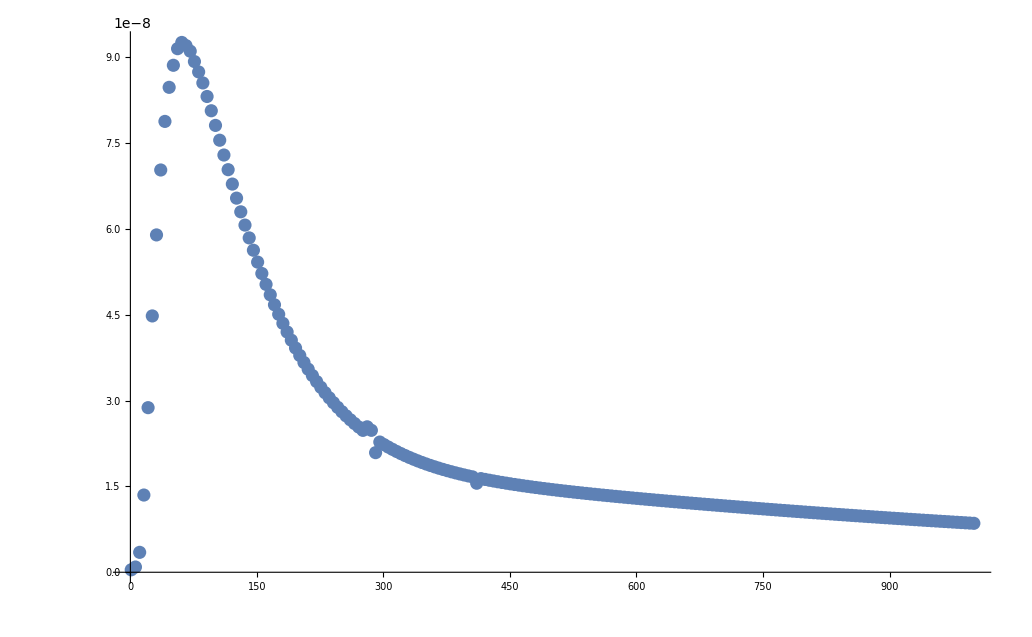

```mathematica
n=200;
dat={#,0,sigmavLowEnergyApproxTemp[points[[1]],Sqrt[points[[1]]["mSsq"]]/#]}&/@Table[Sqrt[points[[1]]["mSsq"]]n/(n+999*x),{x,0,n}] //AbsoluteTiming;
dat[[1]]
dat=dat[[2]]
ListPlot[dat,PlotRange->All]
```

```mathematica
dat={{1,0.16716800100545443},{2,0.2876972329439601},{3,0.34857443862244114},{4,0.37898605351761105},{5,0.392927424186276},{6,0.39775883882609037},{7,0.39745245232340876},{8,0.3942096261637839},{9,0.3892903515291332},{10,0.38343807592832957},{11,0.37710238526939494},{12,0.3705599132496957},{13,0.363982469456442},{14,0.3574767670842497},{15,0.3511082994650239},{16,0.34491606781696543},{17,0.3389218691987357},{18,0.3331362643630019},{19,0.3275624725265099},{20,0.3221989456319997},{21,0.3170410867618391},{22,0.3120824054438964},{23,0.30731529762414617},{24,0.3027315726927059},{25,0.29832280847409826},{26,0.2940805883509632},{27,0.289996657192973},{28,0.28606302116005444},{29,0.28227200866206503},{30,0.2786163044740099},{31,0.2750889653863567},{32,0.27168342326857114},{33,0.2683934796817664},{34,0.26521329495475526},{35,0.2621373737761698},{36,0.25916054874471517},{37,0.25627796288517674},{38,0.2534850518278809},{39,0.2507775261278943},{40,0.24815135404187427},{41,0.24560274496760987},{42,0.2431281336708096},{43,0.24072416536688596},{44,0.2383876816855595},{45,0.2361157075185329},{46,0.23390543873172231},{47,0.23175423071131668},{48,0.22965958770509876},{49,0.2276191529161049},{50,0.22563069930369412},{51,0.22369212104648215},{52,0.22180142562238606},{53,0.21995672646243475},{54,0.21815623613684978},{55,0.2163982600341608},{56,0.21468119049640091},{57,0.21300350137585275},{58,0.211363742981205},{59,0.20976053738323092},{60,0.2081925740523779},{61,0.2066586058027253},{62,0.20515744501881322},{63,0.20368796014333965},{64,0.20224907240631843},{65,0.20083975277696264},{66,0.19945901912104064},{67,0.19810593354887382},{68,0.19677959993924055},{69,0.19547916162615542},{70,0.19420379923644432},{71,0.19295272866701496},{72,0.19172519919157585},{73,0.19052049168749485},{74,0.18933791697400068},{75,0.18817681425388366},{76,0.18703654965132863},{77,0.18591651483906438},{78,0.18481612574864742},{79,0.18373482135809382},{80,0.18267206255157498},{81,0.1816273310462279},{82,0.1806001283815786},{83,0.17958997496738882},{84,0.17859640918601108},{85,0.1776189865456847},{86,0.17665727888146013},{87,0.17571087360062945},{88,0.17477937296983997},{89,0.17386239344120827},{90,0.17295956501498738},{91,0.17207053063650007},{92,0.17119494562520696},{93,0.1703324771339142},{94,0.16948280363630605},{95,0.16864561444107765},{96,0.16782060923103576},{97,0.16700749762575628},{98,0.1662059987663419},{99,0.1654158409209717},{100,0.16463676111012873},{101,0.16386850475024872},{102,0.1631108253148169},{103,0.16236348401192752},{104,0.16162624947728932},{105,0.16089889748195044},{106,0.16018121065379307},{107,0.15947297821212775},{108,0.1587739957146552},{109,0.15808406481609721},{110,0.15740299303789038},{111,0.15673059354837873},{112,0.15606668495288512},{113,0.15541109109319978},{114,0.15476364085598643},{115,0.15412416798961376},{116,0.15349251092901164},{117,0.1528685126281296},{118,0.15225202039961544},{119,0.15164288576135043},{120,0.15104096428950142},{121,0.15044611547776443},{122,0.14985820260249552},{123,0.14927709259345923},{124,0.14870265590986018},{125,0.1481347664215235},{126,0.14757330129483476},{127,0.14701814088332235},{128,0.14646916862261453},{129,0.1459262709295762},{130,0.1453893371054329},{131,0.14485825924269713},{132,0.14433293213572207},{133,0.1438132531947179},{134,0.14329912236307502},{135,0.1427904420378448},{136,0.14228711699323565},{137,0.14178905430699515},{138,0.14129616328954436},{139,0.1408083554157568},{140,0.1403255442592209},{141,0.1398476454290045},{142,0.13937457650861415},{143,0.13890625699722411},{144,0.13844260825304047},{145,0.13798355343866706},{146,0.1375290174683855},{147,0.13707892695735543},{148,0.13663321017254118},{149,0.1361917969854077},{150,0.13575461882623419},{151,0.13532160863994636},{152,0.1348927008435677},{153,0.13446783128503687},{154,0.13404693720345148},{155,0.13362995719064408},{156,0.13321683115404526},{157,0.13280750028076976},{158,0.13240190700291876},{159,0.13199999496398235},{160,0.13160170898637114},{161,0.13120699503998998},{162,0.13081580021181982},{163,0.13042807267649423},{164,0.13004376166780404},{165,0.1296628174510988},{166,0.129285191296573},{167,0.1289108354533933},{168,0.12853970312460763},{169,0.12817174844287094},{170,0.12780692644688277},{171,0.12744519305858554},{172,0.12708650506102218},{173,0.1267308200768917},{174,0.1263780965477409},{175,0.1260282937137941},{176,0.12568137159435527},{177,0.12533729096884288},{178,0.12499601335832158},{179,0.12465750100764582},{180,0.12432171686806032},{181,0.12398862458036383},{182,0.12365818845851984},{183,0.12333037347375296},{184,0.12300514523912763},{185,0.12268246999448966},{186,0.12236231459193599},{187,0.1220446464816245},{188,0.12172943369800195},{189,0.12141664484642677},{190,0.12110624909012797},{191,0.12079821613758915},{192,0.12049251623021216},{193,0.12018912013036075},{194,0.11988799910972435},{195,0.11958912493797544},{196,0.11929246987174784},{197,0.1189980066439294},{198,0.11870570845320566},{199,0.11841554895391976},{200,0.11812750224614325}}
```

{{1,0.167168},{2,0.287697},{3,0.348574},{4,0.378986},{5,0.392927},{6,0.397759},{7,0.397452},{8,0.39421},{9,0.38929},{10,0.383438},{11,0.377102},{12,0.37056},{13,0.363982},{14,0.357477},{15,0.351108},{16,0.344916},{17,0.338922},{18,0.333136},{19,0.327562},{20,0.322199},{21,0.317041},{22,0.312082},{23,0.307315},{24,0.302732},{25,0.298323},{26,0.294081},{27,0.289997},{28,0.286063},{29,0.282272},{30,0.278616},{31,0.275089},{32,0.271683},{33,0.268393},{34,0.265213},{35,0.262137},{36,0.259161},{37,0.256278},{38,0.253485},{39,0.250778},{40,0.248151},{41,0.245603},{42,0.243128},{43,0.240724},{44,0.238388},{45,0.236116},{46,0.233905},{47,0.231754},{48,0.22966},{49,0.227619},{50,0.225631},{51,0.223692},{52,0.221801},{53,0.219957},{54,0.218156},{55,0.216398},{56,0.214681},{57,0.213004},{58,0.211364},{59,0.209761},{60,0.208193},{61,0.206659},{62,0.205157},{63,0.203688},{64,0.202249},{65,0.20084},{66,0.199459},{67,0.198106},{68,0.19678},{69,0.195479},{70,0.194204},{71,0.192953},{72,0.191725},{73,0.19052},{74,0.189338},{75,0.188177},{76,0.187037},{77,0.185917},{78,0.184816},{79,0.183735},{80,0.182672},{81,0.181627},{82,0.1806},{83,0.17959},{84,0.178596},{85,0.177619},{86,0.176657},{87,0.175711},{88,0.174779},{89,0.173862},{90,0.17296},{91,0.172071},{92,0.171195},{93,0.170332},{94,0.169483},{95,0.168646},{96,0.167821},{97,0.167007},{98,0.166206},{99,0.165416},{100,0.164637},{101,0.163869},{102,0.163111},{103,0.162363},{104,0.161626},{105,0.160899},{106,0.160181},{107,0.159473},{108,0.158774},{109,0.158084},{110,0.157403},{111,0.156731},{112,0.156067},{113,0.155411},{114,0.154764},{115,0.154124},{116,0.153493},{117,0.152869},{118,0.152252},{119,0.151643},{120,0.151041},{121,0.150446},{122,0.149858},{123,0.149277},{124,0.148703},{125,0.148135},{126,0.147573},{127,0.147018},{128,0.146469},{129,0.145926},{130,0.145389},{131,0.144858},{132,0.144333},{133,0.143813},{134,0.143299},{135,0.14279},{136,0.142287},{137,0.141789},{138,0.141296},{139,0.140808},{140,0.140326},{141,0.139848},{142,0.139375},{143,0.138906},{144,0.138443},{145,0.137984},{146,0.137529},{147,0.137079},{148,0.136633},{149,0.136192},{150,0.135755},{151,0.135322},{152,0.134893},{153,0.134468},{154,0.134047},{155,0.13363},{156,0.133217},{157,0.132808},{158,0.132402},{159,0.132},{160,0.131602},{161,0.131207},{162,0.130816},{163,0.130428},{164,0.130044},{165,0.129663},{166,0.129285},{167,0.128911},{168,0.12854},{169,0.128172},{170,0.127807},{171,0.127445},{172,0.127087},{173,0.126731},{174,0.126378},{175,0.126028},{176,0.125681},{177,0.125337},{178,0.124996},{179,0.124658},{180,0.124322},{181,0.123989},{182,0.123658},{183,0.12333},{184,0.123005},{185,0.122682},{186,0.122362},{187,0.122045},{188,0.121729},{189,0.121417},{190,0.121106},{191,0.120798},{192,0.120493},{193,0.120189},{194,0.119888},{195,0.119589},{196,0.119292},{197,0.118998},{198,0.118706},{199,0.118416},{200,0.118128}}

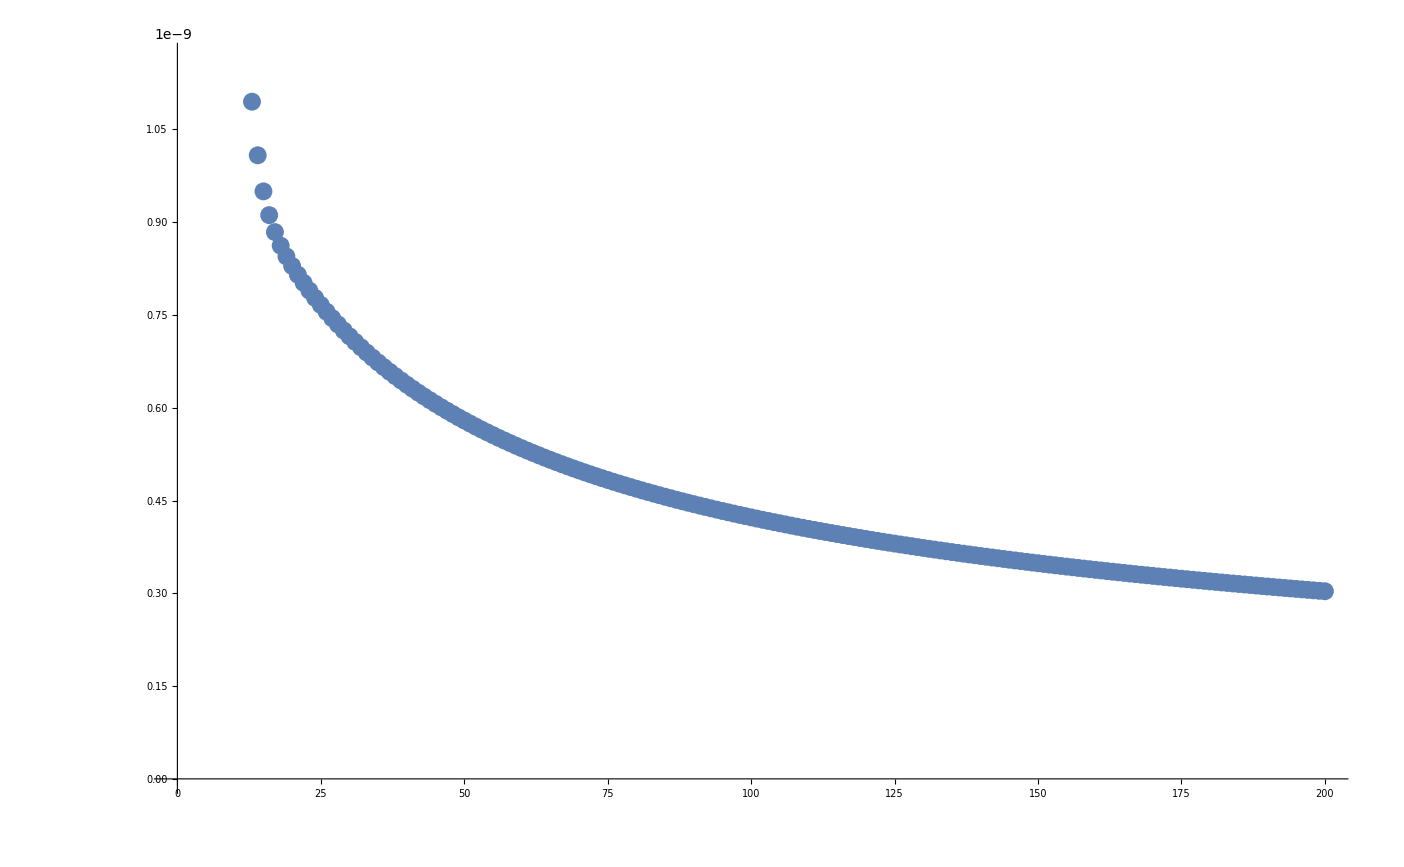

{a→1.60447×10^-10,b→3.39398×10^-8,c→30.6824}

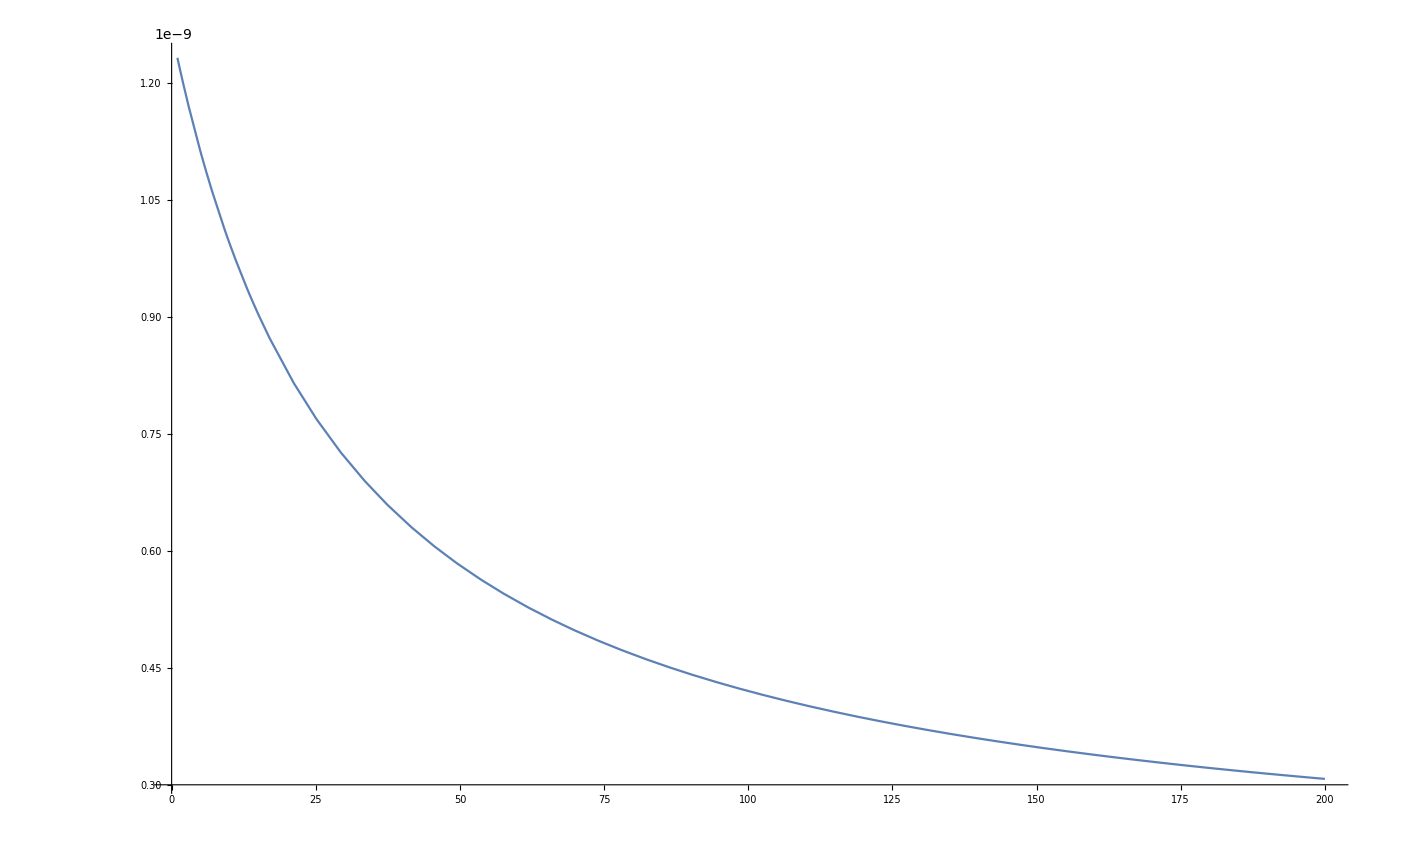

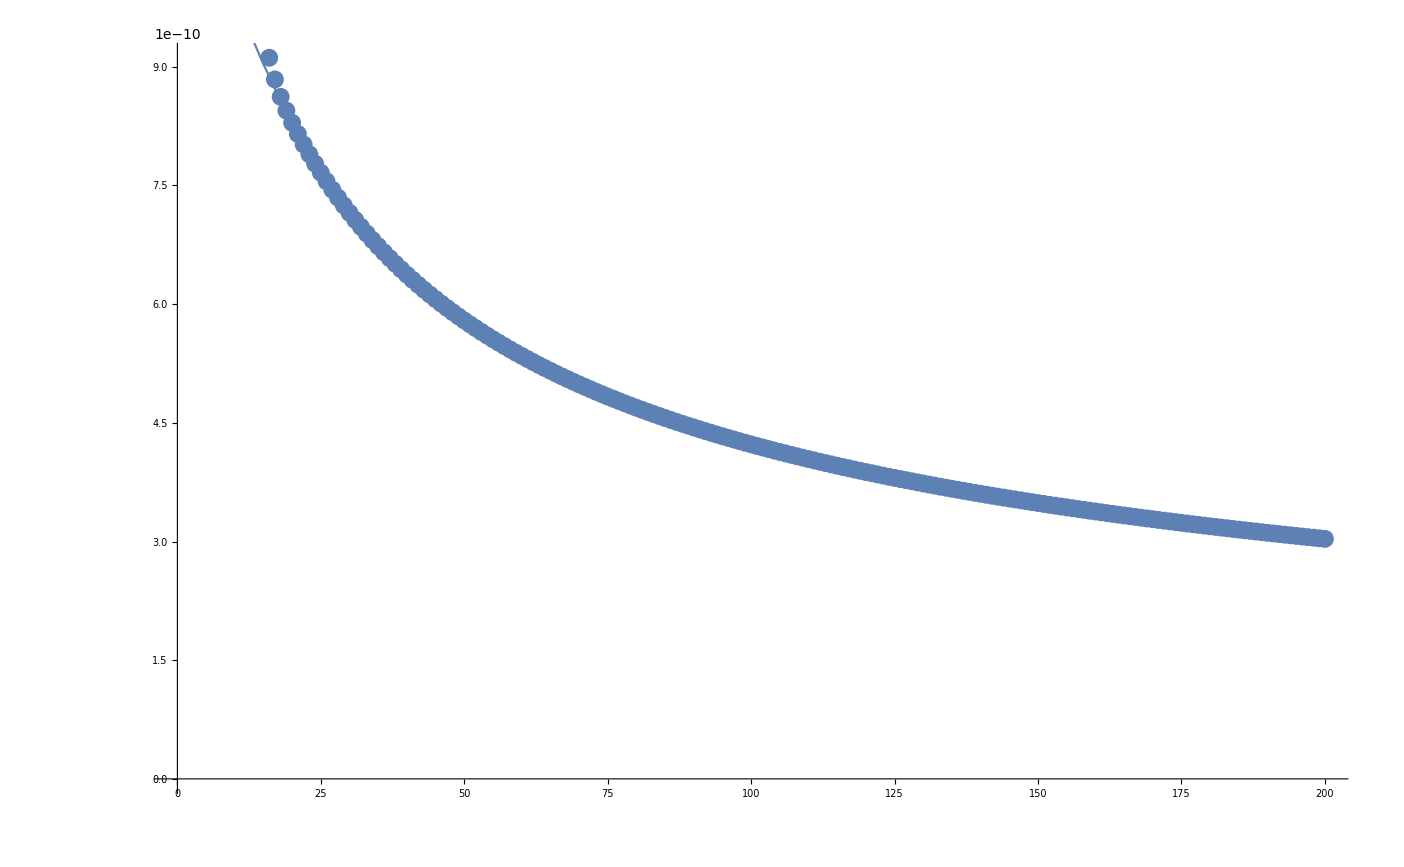

```mathematica
ListPlot[dat]
Clear[a]
Clear[b]
Clear[c]
Clear[d]
Clear[e]

fitDat =Cases[dat,x_/;x[[1]]>15];
fit =FindFit[fitDat,a+b/(x+c),{a,b,c},x]
p1=ListPlot[fitDat];
p2=Plot[(a+b/(x+c))/.fit,{x,1,200}]
Show[{p1,p2}]
```

NIntegrate::precw: The precision of the argument function ((-36197.1 + s)\ « 1 »\ (9.33788×10^-10\ (1.2293/Plus[« 2 »] - 6.03003/Plus[« 2 »])^2\ √s\ Abs[-2. + Plus[« 2 »]\ Plus[« 2 »]]^2 + 0.64\ (0.00883116/Plus[« 2 »] - 0.0433192/Plus[« 2 »])^2\ If[√s < 2.5, 0, gammaHffbar[3, mc, √s]] + 0.316687\ (0.0125543/Plus[« 2 »] - 0.0615822/Plus[« 2 »])^2\ If[√s < 3.55398, 0, gammaHffbar[1, mtau, √s]] + 0.0566893\ (« 1 » « 1 »^2\ If[√s < 8.4, 0, gammaHffbar[3, mb, √s]] + 5.98355×10^-9\ (-42.6484/Plus[« 2 »] - « 18 »/Plus « 1 » « 1 »])^2\ If[√s < 80.398, 0, If[√s ≥ 2\ mW, gammaWWonShell[√s], gammaWWstar[√s]]] + 3.61574×10^-9\ (-54.8635/Plus[« 2 »] - 582.765/Plus[« 2 »])^2\ If[√s < 91.1876, 0, If[√s ≥ 2\ mZ, gammaZZonShell[√s], gammaZZstar[√s]]] + 0.0000330295\ (1.2293/Plus[« 2 »] - 6.03003/Plus[« 2 »])^2\ If[√s < 348., 0, gammaHffbar[3, mt, √s]])) is less than WorkingPrecision (20.).

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in s near {s} = {53841.658369271458665}. NIntegrate obtained 8.5189848189484877914×10^-24 and 2.7203469546601648929×10^-32 for the integral and error estimates.

NIntegrate::precw: The precision of the argument function ((-36197.1 + s)\ « 1 »\ (9.33788×10^-10\ (1.2293/Plus[« 2 »] - 6.03003/Plus[« 2 »])^2\ √s\ Abs[-2. + Plus[« 2 »]\ Plus[« 2 »]]^2 + 0.64\ (0.00883116/Plus[« 2 »] - 0.0433192/Plus[« 2 »])^2\ If[√s < 2.5, 0, gammaHffbar[3, mc, √s]] + 0.316687\ (0.0125543/Plus[« 2 »] - 0.0615822/Plus[« 2 »])^2\ If[√s < 3.55398, 0, gammaHffbar[1, mtau, √s]] + 0.0566893\ (« 1 » « 1 »^2\ If[√s < 8.4, 0, gammaHffbar[3, mb, √s]] + 5.98355×10^-9\ (-42.6484/Plus[« 2 »] - « 18 »/Plus « 1 » « 1 »])^2\ If[√s < 80.398, 0, If[√s ≥ 2\ mW, gammaWWonShell[√s], gammaWWstar[√s]]] + 3.61574×10^-9\ (-54.8635/Plus[« 2 »] - 582.765/Plus[« 2 »])^2\ If[√s < 91.1876, 0, If[√s ≥ 2\ mZ, gammaZZonShell[√s], gammaZZstar[√s]]] + 0.0000330295\ (1.2293/Plus[« 2 »] - 6.03003/Plus[« 2 »])^2\ If[√s < 348., 0, gammaHffbar[3, mt, √s]])) is less than WorkingPrecision (20.).

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in s near {s} = {43441.784660617736586}. NIntegrate obtained 6.3667525521048083801×10^-42 and 2.5734655663137140384×10^-51 for the integral and error estimates.

NIntegrate::precw: The precision of the argument function ((-36197.1 + s)\ « 1 »\ (9.33788×10^-10\ (1.2293/Plus[« 2 »] - 6.03003/Plus[« 2 »])^2\ √s\ Abs[-2. + Plus[« 2 »]\ Plus[« 2 »]]^2 + 0.64\ (0.00883116/Plus[« 2 »] - 0.0433192/Plus[« 2 »])^2\ If[√s < 2.5, 0, gammaHffbar[3, mc, √s]] + 0.316687\ (0.0125543/Plus[« 2 »] - 0.0615822/Plus[« 2 »])^2\ If[√s < 3.55398, 0, gammaHffbar[1, mtau, √s]] + 0.0566893\ (« 1 » « 1 »^2\ If[√s < 8.4, 0, gammaHffbar[3, mb, √s]] + 5.98355×10^-9\ (-42.6484/Plus[« 2 »] - « 18 »/Plus « 1 » « 1 »])^2\ If[√s < 80.398, 0, If[√s ≥ 2\ mW, gammaWWonShell[√s], gammaWWstar[√s]]] + 3.61574×10^-9\ (-54.8635/Plus[« 2 »] - 582.765/Plus[« 2 »])^2\ If[√s < 91.1876, 0, If[√s ≥ 2\ mZ, gammaZZonShell[√s], gammaZZstar[√s]]] + 0.0000330295\ (1.2293/Plus[« 2 »] - 6.03003/Plus[« 2 »])^2\ If[√s < 348., 0, gammaHffbar[3, mt, √s]])) is less than WorkingPrecision (20.).

General::stop: Further output of NIntegrate :: precw will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in s near {s} = {39751.408602131203524}. NIntegrate obtained 9.7816554309775868943×10^-60 and 1.7793375781524638429×10^-69 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

62.6376

{{20,0.322199},{40,0.248151},{60,0.208193},{80,0.182672},{100,0.164637},{120,0.151041},{140,0.140326},{160,0.131602},{180,0.124322},{200,0.118128}}

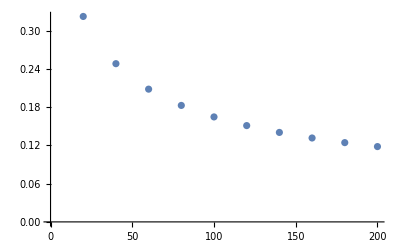

```mathematica
n=10;
dat ={#,sigmavSchannelSMTemp[points[[1]],Sqrt[points[[1]]["mSsq"]]/#]*0.3894*10^9}&/@Table[200/n*x,{x,1,n}] //AbsoluteTiming;
dat[[1]]
dat=dat[[2]]
ListPlot[dat]
fitDat =Cases[dat,x_/;x[[1]]>7];
fit =FindFit[fitDat,a+b/(x+c),{a,b,c},x]
p1=ListPlot[fitDat];
p2=Plot[(a+b/(x+c))/.fit,{x,1,200}];
Show[{p1,p2}]
```

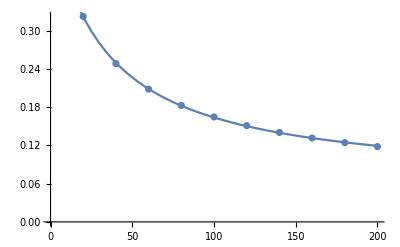

```mathematica
{a->0.060296126258005935,b->13.70427729911952,c->32.42966076470842}
```

```mathematica
({a,b,c}/.{a->0.060723611847101934,b->13.64594849059883,c->32.34088404954129} )-( {a,b,c}/.{a->0.060296126258005935,b->13.70427729911952,c->32.42966076470842})
```

{0.000427486,-0.0583288,-0.0887767}

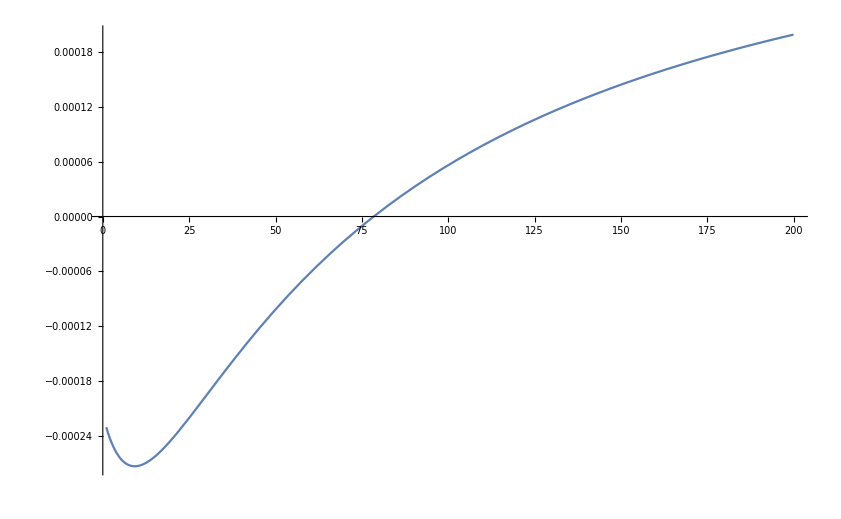

```mathematica
p1=Plot[((a+b/(x+c))/.{a->0.060723611847101934,b->13.64594849059883,c->32.34088404954129} )-((a+b/(x+c))/.{a->0.060296126258005935,b->13.70427729911952,c->32.42966076470842}),{x,1,200}]
```

```mathematica
p1={Sqrt[s]/2,0,0,Sqrt[s/4-mss^2]};
p2={Sqrt[s]/2,0,0,-Sqrt[s/4-mss^2]};
k1={e,Sin[t]Sqrt[e^2-mh1^2],0,Cos[t]Sqrt[e^2-mh1^2]};
k2={Sqrt[e^2-mh1^2+mh2^2],-Sin[t]Sqrt[e^2-mh1^2],0,-Cos[t]Sqrt[e^2-mh1^2]}

e=(mh1^2-mh2^2+s)/(2 √s);
(*p1
k1=Simplify[k1,Assumptions->{0<mh1<mh2,mss>0,s>0}]
k2=Simplify[k2,Assumptions->{0<mh1<mh2,mss>0,s>0}]
d1=FullSimplify[(p1-k1).(p1-k1)-mss^2,Assumptions->{0<mh1<mh2,mss>0,s>0}]
d2=FullSimplify[(p2-k1).(p2-k1)-mss^2,Assumptions->{0<mh1<mh2,mss>0,s>0}]
FullSimplify[1/d1+1/d2]
*)
```

{√(-mh1^2+mh2^2+((mh1^2-mh2^2+s)^2)/(4 s)),-√(-mh1^2+((mh1^2-mh2^2+s)^2)/(4 s)) Sin[t],0,-√(-mh1^2+((mh1^2-mh2^2+s)^2)/(4 s)) Cos[t]}

```mathematica
p1.{{1,0,0,0},{0,-1,0,0},{0,0,-1,0},{0,0,0,-1}}.p1
p2.{{1,0,0,0},{0,-1,0,0},{0,0,-1,0},{0,0,0,-1}}.p2
Simplify[k1.{{1,0,0,0},{0,-1,0,0},{0,0,-1,0},{0,0,0,-1}}.k1]
Simplify[k2.{{1,0,0,0},{0,-1,0,0},{0,0,-1,0},{0,0,0,-1}}.k2]
d1=Simplify[(p1-k1).{{1,0,0,0},{0,-1,0,0},{0,0,-1,0},{0,0,0,-1}}.(p1-k1)-mss^2,Assumptions->{0<mh1<mh2,mss>0,s>0}]
d2=Simplify[(p2-k1).{{1,0,0,0},{0,-1,0,0},{0,0,-1,0},{0,0,0,-1}}.(p2-k1)-mss^2,Assumptions->{0<mh1<mh2,mss>0,s>0}]
Simplify[(1/d1+1/d2)]
```

mss^2

mss^2

mh1^2

mh2^2

1/2 (mh1^2+mh2^2-s+√(-4 mss^2+s) √((mh1^4+(mh2^2-s)^2-2 mh1^2 (mh2^2+s))/s) Cos[t])

1/2 (mh1^2+mh2^2-s-√(-4 mss^2+s) √((mh1^4+(mh2^2-s)^2-2 mh1^2 (mh2^2+s))/s) Cos[t])

2/(mh1^2+mh2^2-s-√(-4 mss^2+s) √((mh1^4+(mh2^2-s)^2-2 mh1^2 (mh2^2+s))/s) Cos[t])+2/(mh1^2+mh2^2-s+√(-4 mss^2+s) √((mh1^4+(mh2^2-s)^2-2 mh1^2 (mh2^2+s))/s) Cos[t])

```mathematica
FullSimplify[2/((mh1^2+mh2^2-s)^2-(√(-4 mss^2+s) √((mh1^4+(mh2^2-s)^2-2 mh1^2 (mh2^2+s))/s) Cos[t])^2)]
```

```mathematica
(2s)/(s(mh1^2+mh2^2-s)^2+(4 mss^2-s) (mh1^4+(mh2^2-s)^2-2 mh1^2 (mh2^2+s)) Cos[t]^2)
```

(2 s)/((mh1^2+mh2^2-s)^2 s+(4 mss^2-s) (mh1^4+(mh2^2-s)^2-2 mh1^2 (mh2^2+s)) Cos[t]^2)

```mathematica
Simplify[2/((mh1^2+mh2^2-s)^2+((4 mss^2-s) (mh1^4+(mh2^2-s)^2-2 mh1^2 (mh2^2+s)) Cos[t]^2)/s)/.s->(mh1+mh2)^2]
```

1/(2 mh1^2 mh2^2)

```mathematica
Solve[(k1+k2).{{1,0,0,0},{0,-1,0,0},{0,0,-1,0},{0,0,0,-1}}.(k1+k2)==s,e]
```

{{e→(-mh1^2+mh2^2-s)/(2 √s)},{e→(mh1^2-mh2^2+s)/(2 √s)}}

```mathematica
Integrate[(a+b/(c^2-g^2*x^2))^2,{x,-1,1},Assumptions->{a>0,b>0,c>0,g>0}]
```

ConditionalExpression[(2 c g (b^2+2 a^2 c^2 (c^2-g^2))-b (b+4 a c^2) (c^2-g^2) Log[(c-g)/(c+g)])/(2 c^3 g (c^2-g^2)),c≥g]

```mathematica
Expand[(2 c g (b^2+2 a^2 c^2 (c^2-g^2))-b (b+4 a c^2) (c^2-g^2) Log[(c-g)/(c+g)])/(2 c^3 g (c^2-g^2))]
```

```mathematica
b^2/(c^2 (c^2-g^2))+2 a^2+(b (b+4 a c^2)  ArcTanh[g/c])/(c^3 g)
```

```mathematica
Simplify[((2 c g (b^2+2 a^2 c^2 (c^2-g^2))-b (b+4 a c^2) (c^2-g^2) TrigToExp[ExpToTrig[Log[(c-g)/(c+g)]]])/(2 c^3 g (c^2-g^2))-(b^2/(c^2 (c^2-g^2))+2 a^2+(-b (b+4 a c^2) (1/2 Log[(c-g)/(c+g)]))/(c^3 g)))]
```

0

```mathematica
ExpToTrig[Log[(c-g)/(c+g)]]
```

Log[(c-g)/(c+g)]

```mathematica
p1.{{1,0,0,0},{0,-1,0,0},{0,0,-1,0},{0,0,0,-1}}.k1
```

1/4 (mh1^2-mh2^2+s)-√(-mss^2+s/4) √(-mh1^2+((mh1^2-mh2^2+s)^2)/(4 s)) Cos[t]

```mathematica
"one over three is " <> ToString[N[1/3]]
```

one over three is 0.333333

```mathematica
calculateRelicDensity[points[[1]]]
```

mass:

95.1276

lambda a:

0.258228

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in s near {s} = {53812.2}. NIntegrate obtained 7.38478×10^-15 and 3.42147×10^-17 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in s near {s} = {53812.2}. NIntegrate obtained 2.07608×10^-7 and 8.85717×10^-9 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in s near {s} = {53812.2}. NIntegrate obtained 0.000451845 and 0.0000127886 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

Relic:

0.00115391

0.00115391

```mathematica
Print["C:\\Users\\AlexandrePoulin\\Documents\\relic\\freezeout_v2.2\\bin\\main "<>ToString[ N[Sqrt[points[[1]]["mSsq"]]] ]]
Run["C:\\Users\\AlexandrePoulin\\Documents\\relic\\freezeout_v2.2\\bin\\main "<>ToString[ N[Sqrt[points[[1]]["mSsq"]]] ] ];
relic = Flatten[ReadList[relicFilePath,{Number}]]
If[failMessages,Print["Relic:"]; Print[relic]];
relic
```

C:\Users\AlexandrePoulin\Documents\relic\freezeout_v2.2\bin\main 95.1276

{}

Relic:

{}

{}

```mathematica
relic = Flatten[ReadList[relicFilePath,{Number}]][[1]]
Print[relic];
```

5.72922×10^-7

5.72922×10^-7

```mathematica
n=100;
m=10;
(*Print["lambda_a "<>ToString[N[p["lambda_a"]]]];*)

(*dat1={Sqrt[points[[1]]["mSsq"]]/#,sigmavLowEnergyApproxTemp[points[[1]],#]}&/@Table[Sqrt[points[[1]]["mSsq"]]n/(n+999*x),{x,0,100}]*)
datx={Sqrt[points[[1]]["mSsq"]]/#,sigmavLowEnergyApproxTemp[points[[1]],#]}&/@Table[Sqrt[points[[1]]["mSsq"]]m/(m+999*x),{x,2,m}];
fit =FindFit[datx,fita+fitb/(x+fitc),{fita,fitb,fitc},x];
plot=Plot[(fita+fitb/(x+fitc))/.fit,{x,0,1000}];
dat2={#,0,If[Sqrt[points[[1]]["mSsq"]]/#<200,sigmavLowEnergyApproxTemp[points[[1]],#],(fita+fitb/(Sqrt[points[[1]]["mSsq"]]/#+fitc))/.fit]}&/@Table[Sqrt[points[[1]]["mSsq"]]n/(n+999*x),{x,0,100}];
Export[mathematicaOut,dat2,"Table"];
Run["C:\\Users\\AlexandrePoulin\\Documents\\relic\\freezeout_v2.2\\bin\\main "<>ToString[ N[Sqrt[points[[1]]["mSsq"]]] ] ];
relic = Flatten[ReadList[relicFilePath,{Number}]][[1]]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in s near {s} = {707768.}. NIntegrate obtained 31.5632 and 0.0771384 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in s near {s} = {53882.5}. NIntegrate obtained 0.598317 and 0.0695221 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in s near {s} = {54024.2}. NIntegrate obtained 0.317846 and 0.00061978 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

0.347329

```mathematica
0.347329
```

0.347329

```mathematica
sigmavLowEnergyApproxTemp1[para_,T_]:=T/(32*Pi^4*neq[para,T]^2)*NIntegrate[Abs[sigmavSchannelSMTemp[para,s]]*(s-4para["mSsq"])Sqrt[s]*BesselK[1,Sqrt[s]/T],{s,4*para["mSsq"],Infinity}]
sigmavLowEnergyApproxTemp2[para_,T_]:=T/(32*Pi^4*neq[para,T]^2)*NIntegrate[Abs[sigmavSchannelH3VTemp[para,s]]*(s-4para["mSsq"])Sqrt[s]*BesselK[1,Sqrt[s]/T],{s,4*para["mSsq"],Infinity}]
sigmavLowEnergyApproxTemp3[para_,T_]:=T/(32*Pi^4*neq[para,T]^2)*NIntegrate[Abs[sigmav4PointTemp[para,s]]*(s-4para["mSsq"])Sqrt[s]*BesselK[1,Sqrt[s]/T],{s,4*para["mSsq"],Infinity}]
sigmavLowEnergyApproxTemp4[para_,T_]:=T/(32*Pi^4*neq[para,T]^2)*NIntegrate[Abs[sigmavTchannelTemp[para,s]]*(s-4para["mSsq"])Sqrt[s]*BesselK[1,Sqrt[s]/T],{s,4*para["mSsq"],Infinity}]
sigmavLowEnergyApproxTemp5[para_,T_]:=T/(32*Pi^4*neq[para,T]^2)*NIntegrate[Abs[sigmavUchannelTemp[para,s]]*(s-4para["mSsq"])Sqrt[s]*BesselK[1,Sqrt[s]/T],{s,4*para["mSsq"],Infinity}]
0.1/(32*Pi^4*neq[points[[1]],0.1]^2)*NIntegrate[Abs[sigmavSchannelSMTemp[points[[1]],s]](s-4points[[1]]["mSsq"])Sqrt[s]*BesselK[1,Sqrt[s]/0.1],{s,4*points[[1]]["mSsq"],2*4*points[[1]]["mSsq"]}]

points[[1]]["mSsq"]^0.5
sigmavLowEnergyApproxTemp1[points[[1]],0.1]
```

0.

95.1276

0.

```mathematica
dat2
```

{{1.,31.5632,0.243252},{10.99,0.598317,0.22934},{20.98,0.317846,0.217103},{30.97,0.275193,0.206255},{40.96,0.245703,0.196573},{50.95,0.223788,0.187877},{60.94,0.20675,0.180025},{70.93,0.19304,0.1729},{80.92,0.18171,0.166405},{90.91,0.17215,0.16046},{100.9,0.163945,0.154998},{110.89,0.156804,0.149962},{120.88,0.150517,0.145305},{130.87,0.144927,0.140985},{140.86,0.139914,0.136967},{150.85,0.135386,0.13322},{160.84,0.13127,0.129718},{170.83,0.127506,0.126438},{180.82,0.124048,0.123358},{190.81,0.120857,0.120462},{200.8,Null,0.117733},{210.79,Null,0.115158},{220.78,Null,0.112723},{230.77,Null,0.110418},{240.76,Null,0.108232},{250.75,Null,0.106156},{260.74,Null,0.104183},{270.73,Null,0.102304},{280.72,Null,0.100514},{290.71,Null,0.0988054},{300.7,Null,0.0971737},{310.69,Null,0.0956135},{320.68,Null,0.0941202},{330.67,Null,0.0926897},{340.66,Null,0.091318},{350.65,Null,0.0900016},{360.64,Null,0.0887372},{370.63,Null,0.0875218},{380.62,Null,0.0863527},{390.61,Null,0.0852271},{400.6,Null,0.0841427},{410.59,Null,0.0830974},{420.58,Null,0.0820889},{430.57,Null,0.0811155},{440.56,Null,0.0801753},{450.55,Null,0.0792666},{460.54,Null,0.0783879},{470.53,Null,0.0775377},{480.52,Null,0.0767147},{490.51,Null,0.0759176},{500.5,Null,0.0751451},{510.49,Null,0.0743962},{520.48,Null,0.0736698},{530.47,Null,0.0729648},{540.46,Null,0.0722804},{550.45,Null,0.0716157},{560.44,Null,0.0709698},{570.43,Null,0.0703419},{580.42,Null,0.0697313},{590.41,Null,0.0691373},{600.4,Null,0.0685592},{610.39,Null,0.0679964},{620.38,Null,0.0674484},{630.37,Null,0.0669144},{640.36,Null,0.066394},{650.35,Null,0.0658867},{660.34,Null,0.065392},{670.33,Null,0.0649094},{680.32,Null,0.0644384},{690.31,Null,0.0639788},{700.3,Null,0.06353},{710.29,Null,0.0630917},{720.28,Null,0.0626635},{730.27,Null,0.0622451},{740.26,Null,0.0618361},{750.25,Null,0.0614363},{760.24,Null,0.0610453},{770.23,Null,0.0606628},{780.22,Null,0.0602885},{790.21,Null,0.0599223},{800.2,Null,0.0595638},{810.19,Null,0.0592128},{820.18,Null,0.0588691},{830.17,Null,0.0585324},{840.16,Null,0.0582026},{850.15,Null,0.0578794},{860.14,Null,0.0575626},{870.13,Null,0.057252},{880.12,Null,0.0569475},{890.11,Null,0.0566488},{900.1,Null,0.0563559},{910.09,Null,0.0560685},{920.08,Null,0.0557865},{930.07,Null,0.0555098},{940.06,Null,0.0552381},{950.05,Null,0.0549714},{960.04,Null,0.0547096},{970.03,Null,0.0544524},{980.02,Null,0.0541998},{990.01,Null,0.0539516},{1000.,Null,0.0537077}}

```mathematica
test2=<|"mhsq"->15625.,"mHsq"->808486.0299603791,"m3sq"->808624.5376421922,"m5sq"->809839.256382043,"mSsq"->6817.326273363253,"kf"->0.9984401402920013,"kV"->1.0043212292468777,"mu2sq"->-7864.99491707422,"mu3sq"->795939.3437167127,"muSsq"->-84050.06587535731,"lambda_1"->0.04688683511469731,"lambda_2"->0.08930031525544369,"lambda_3"->0.14851509667204343,"lambda_4"->0.32073460527320485,"lambda_5"->0.1660612488451747,"lambda_a"->0.7520634831144918,"lambda_b"->0.7743865503748311,"lambda_s"->1.2769706435752295,"M_1"->348.7890577295466,"M_2"->-53.57155513458474,"v_chi"->6.578343439260687,"v_phi"->245.51654081880577,"ca"->0.9955852607341421,"sa"->-0.09386153956190119,"cH"->0.9971406602733096,"sH"->0.0755678743230745,"gSSh"->-16.389258763031318,"gSSH"->-33.280250631944014,"gSShh"->-3.009040596331087,"gSSHH"->-3.096759537626205,"gSShH"->-0.008344109428481034,"gSSH30H30"->-3.0970362976728585,"gSSH50H50"->-3.0975462014993242,"gSSH3pH3n"->-3.0970362976728585,"gSSH5pH5n"->-3.0975462014993242,"GSSH5ppH5nn"->-3.0975462014993242,"ghtt"->0.7055811180379409,"gHtt"->-0.06652060113466635,"ghbb"->0.017031268366433056,"gHbb"->-0.001605669682560912,"ghcc"->0.0050688298709622185,"gHcc"->-0.0004778778817145571,"ghtautau"->0.007205807993920923,"gHtautau"->-0.0006793473736223607,"ghuu"->8.921140572893505*^-6,"gHuu"->-8.410650718176205*^-7,"ghee"->2.072137651249355*^-6,"gHee"->-1.953564780449109*^-7,"ghmumu"->0.00042844994120490087,"gHmumu"->-0.00004039329698095734,"ghWW"->52.73133886406501,"gHWW"->1.5364839480588874,"ghZZ"->67.83438294576995,"gHZZ"->1.9765559298871245,"ghH3W"->0.025339490761187453,"gHH3W"->0.5316626836174919,"ghH3Z"->0.028740109800428584,"gHH3Z"->0.6030130616263889,"ghH3H3"->105.20991011890229,"gHH3H3"->223.52737936805377,"ghH5H5"->114.49862252952845,"gHH5H5"->-154.23207914027265,"ghhh"->188.34533130493125,"ghhH"->-898.4776262524035,"ghHH"->220.1508202837614,"gHHH"->456.2824713641478,"bsgPass"->True,"m3Pass"->True,"m5Pass"->True,"relic"->0.110027|>
```

<|mhsq→15625.,mHsq→808486.,m3sq→808625.,m5sq→809839.,mSsq→6817.33,kf→0.99844,kV→1.00432,mu2sq→-7864.99,mu3sq→795939.,muSsq→-84050.1,lambda_1→0.0468868,lambda_2→0.0893003,lambda_3→0.148515,lambda_4→0.320735,lambda_5→0.166061,lambda_a→0.752063,lambda_b→0.774387,lambda_s→1.27697,M_1→348.789,M_2→-53.5716,v_chi→6.57834,v_phi→245.517,ca→0.995585,sa→-0.0938615,cH→0.997141,sH→0.0755679,gSSh→-16.3893,gSSH→-33.2803,gSShh→-3.00904,gSSHH→-3.09676,gSShH→-0.00834411,gSSH30H30→-3.09704,gSSH50H50→-3.09755,gSSH3pH3n→-3.09704,gSSH5pH5n→-3.09755,GSSH5ppH5nn→-3.09755,ghtt→0.705581,gHtt→-0.0665206,ghbb→0.0170313,gHbb→-0.00160567,ghcc→0.00506883,gHcc→-0.000477878,ghtautau→0.00720581,gHtautau→-0.000679347,ghuu→8.92114×10^-6,gHuu→-8.41065×10^-7,ghee→2.07214×10^-6,gHee→-1.95356×10^-7,ghmumu→0.00042845,gHmumu→-0.0000403933,ghWW→52.7313,gHWW→1.53648,ghZZ→67.8344,gHZZ→1.97656,ghH3W→0.0253395,gHH3W→0.531663,ghH3Z→0.0287401,gHH3Z→0.603013,ghH3H3→105.21,gHH3H3→223.527,ghH5H5→114.499,gHH5H5→-154.232,ghhh→188.345,ghhH→-898.478,ghHH→220.151,gHHH→456.282,bsgPass→True,m3Pass→True,m5Pass→True,relic→0.110027|>

```mathematica
NumberQ[$Failed]
```

False

```mathematica
g
```

(4550.8-$44390) (6.41438×10^11+(800898.-$44390)^2-1.6018×10^6 (800898.+$44390))

```mathematica
conversionFactor3
```

3.894×10^8

```mathematica
g
```

(23851.8-$6909) (2.44141×10^8+(442082.-$6909)^2-31250. (442082.+$6909))

```mathematica
test =StartProcess[{"C:\\Users\\AlexandrePoulin\\Documents\\relic\\freezeout_v2.2\\bin\\main",ToString[ N[Sqrt[test2["mSsq"]]] ]} ];
ProcessStatus[test]
ProcessStatus[test]
```

Running

Running

```mathematica
ReadString[test]
```

EndOfFile

```mathematica
ToString[ N[Sqrt[test["mSsq"]]] ]
```

Sqrt[ProcessObject[7.][mSsq]]

```mathematica
ProcessStatus[test]=="Finished"
```

True

```mathematica
points
```

$Failed

```mathematica
2/((mh1^2+mh2^2-s)^2-(√(-4 mss^2+s) √((mh1^4+(mh2^2-s)^2-2 mh1^2 (mh2^2+s))/s) Cos[t])^2)
```

```mathematica
Simplify[((2(mh1^2+mh2^2-s+√(-4 mss^2+s) √((mh1^4+(mh2^2-s)^2-2 mh1^2 (mh2^2+s))/s) Cos[t])+2(mh1^2+mh2^2-s-√(-4 mss^2+s) √((mh1^4+(mh2^2-s)^2-2 mh1^2 (mh2^2+s))/s) Cos[t]))/((mh1^2+mh2^2-s-√(-4 mss^2+s) √((mh1^4+(mh2^2-s)^2-2 mh1^2 (mh2^2+s))/s) Cos[t])(mh1^2+mh2^2-s+√(-4 mss^2+s) √((mh1^4+(mh2^2-s)^2-2 mh1^2 (mh2^2+s))/s) Cos[t])))]
```

(4 (mh1^2+mh2^2-s))/((mh1^2+mh2^2-s-√(-4 mss^2+s) √((mh1^4+(mh2^2-s)^2-2 mh1^2 (mh2^2+s))/s) Cos[t]) (mh1^2+mh2^2-s+√(-4 mss^2+s) √((mh1^4+(mh2^2-s)^2-2 mh1^2 (mh2^2+s))/s) Cos[t]))

```mathematica
Expand[mh1^4+(mh2^2-s)^2-2 mh1^2 (mh2^2+s)]
```

```mathematica
(mh1^2-mh2^2)^2-(2 mh1^2 +2 mh2^2 )s+s^2
```

```mathematica
Simplify[mh1^4-2 mh1^2 mh2^2+mh2^4]
```

(mh1^2-mh2^2)^2

```mathematica
Integrate[(a-b/(c^2-g^2*x^2))^2,{x,-1,1},Assumptions->{a>0,b>0,c>0,g>0}]
```

ConditionalExpression[(4 a^2 c^3+(2 b^2 c)/(c^2-g^2)-(b (b-4 a c^2) Log[-1+(2 c)/(c+g)])/g)/(2 c^3),c≥g]

```mathematica
Expand[(4 a^2 c^3+(2 b^2 c)/(c^2-g^2)-(b (b-4 a c^2) Log[-1+(2 c)/(c+g)])/g)/(2 c^3)]
```

2 a^2+b^2/(c^2 (c^2-g^2))-(b^2 Log[-1+(2 c)/(c+g)])/(2 c^3 g)+(2 a b Log[-1+(2 c)/(c+g)])/(c g)

```mathematica
2 a^2+b^2/(c^2 (c^2-g^2))+((b^2-4 a b c^2 )ArcTanh[g/c])/(c^3 g)
```

```mathematica
ExpToTrig[Log[(c+g)/(c-g)]]
```

Log[(c-g)/(c+g)]

```mathematica
p=test2;
min = NMinimize[v/.{mu2sq->p["mu2sq"],mu3sq->p["mu3sq"],mussq->p["muSsq"],lam1->p["lambda_1"],lam2->p["lambda_2"],lam3->p["lambda_3"],lam4->p["lambda_4"],lam5->p["lambda_5"],lama->p["lambda_a"],lamb->p["lambda_b"],lams->p["lambda_s"],zeta->zetaRepGood,omega->omegaRepGood,sigma->sigmaRepGood,rho->rhoRepGood,m1->p["M_1"],m2->p["M_1"]},{x,y,z}]
minima={x,y/Sqrt[3],z}/.min[[2]]
Abs[minima[[2]]-p["v_chi"]]<10^(-6) ∧Abs[minima[[1]]-p["v_phi"]]∧Abs[minima[[3]]]<10^(-6)
```

NMinimize::cvdiv: Failed to converge to a solution. The function may be unbounded.

{-3.4576×10^8,{x→-1.57772×10^-30,y→0.,z→-128.277}}

{-1.57772×10^-30,0.,-128.277}

False

NMinimize::nnum: The function value 0.0333098\ (lam1 + 195.256\ (0.986352\ lam3 + lam4) + 13.9734\ (lam2 - 0.0600774\ lam5)) + 0.291461\ (-0.278423\ m1 - 0.286561\ m2) + 0.0912549\ (mu2sq + 13.9734\ mu3sq) is not a number at {g, r, t} = {1.3094, 1.65312, 0.0829166}.

General::stop: Further output of NMinimize :: nnum will be suppressed during this calculation.

False

```mathematica
Sqrt[3]
```

```mathematica
{-1.1763209036296977*^8,{x->245.99830676965988,y->4.746415955756726,z->0.,the->2432.5480304966245}}
{246.09287951908263,2.8031964985864786,0,0.9553166181245092}
```

```mathematica
vevCheck[p_]:=Module[{min,minima},
zetaRepGood = 1/2*(Sin[the])^4+(Cos[the])^4;
omegaRepGood = 1/4*(Sin[the])^2+1/Sqrt[2]*Sin[the]*Cos[the];
sigmaRepGood =1/(2*Sqrt[2])*Sin[the]+1/4*Cos[the];
rhoRepGood =3*(Sin[the])^2*Cos[the];min = NMinimize[{v/.{mu2sq->p["mu2sq"],mu3sq->p["mu3sq"],mussq->p["muSsq"],lam1->p["lambda_1"],lam2->p["lambda_2"],lam3->p["lambda_3"],lam4->p["lambda_4"],lam5->p["lambda_5"],lama->p["lambda_a"],lamb->p["lambda_b"],lams->p["lambda_s"],zeta->(1/2*(Sin[the])^4+(Cos[the])^4),omega->(1/4*(Sin[the])^2+1/Sqrt[2]*Sin[the]*Cos[the]),sigma->(1/(2*Sqrt[2])*Sin[the]+1/4*Cos[the]),rho->(3*(Sin[the])^2*Cos[the]),m1->p["M_1"],m2->p["M_1"]},0≤ the≤2Pi},{x,y,z, the}];
minima={x,y/Sqrt[3],z, the}/.min[[2]];
Print[min];
Print[{p["v_phi"],p["v_chi"],0,theta}];
Abs[minima[[2]]-p["v_chi"]]<10^(-6) ∧Abs[minima[[1]]-p["v_phi"]]∧Abs[minima[[3]]]<10^(-6)
]
```

```mathematica
{-1.0880856736249444*^8,{x->244.7523361975959,y->11.736551506826768,z->2.9369934256241994*^-15,the->0.9553166207618379}}
```

{245.405,7.07744,0,0.955317}

Failed vev check

```mathematica
p=<|"mhsq"->15624.999999999942,"mHsq"->865208.574612058,"m3sq"->780402.8013305082,"m5sq"->608781.9839144648,"mSsq"->7515.42982535467,"kf"->0.9992828357660024,"kV"->1.0060484634733922,"mu2sq"->-6989.534543057565,"mu3sq"->689444.2742656004,"muSsq"->-39717.37797662109,"lambda_1"->0.05077166965668917,"lambda_2"->0.009910255272512991,"lambda_3"->1.1451665152399437,"lambda_4"->-0.17201996238323192,"lambda_5"->-1.082089693443777,"lambda_a"->0.39456593290952235,"lambda_b"->-0.4480271962013506,"lambda_s"->0.18813451683732252,"M_1"->440.9622058154537,"M_2"->-1016.6875985016741,"v_chi"->8.218467582879224,"v_phi"->245.12083338546427,"ca"->0.994819573411218,"sa"->-0.10165636407978747,"cH"->0.9955335344558748,"sH"->0.09440858951278419,"gSSh"->-15.497000468502796,"gSSH"->26.696737407299672,"gSShh"->-1.5434342469208706,"gSSHH"->1.757279300088184,"gSShH"->0.3408448988134279,"gSSH30H30"->1.762068715995447,"gSSH50H50"->1.7921087848054025,"gSSH3pH3n"->1.762068715995447,"gSSH5pH5n"->1.7921087848054025,"GSSH5ppH5nn"->1.7921087848054025,"ghtt"->0.7061766369786532,"gHtt"->-0.07216117498290105,"ghbb"->0.017045642961553698,"gHbb"->-0.001741821465104508,"ghcc"->0.005073108024271933,"gHcc"->-0.0005183992455668179,"ghtautau"->0.007211889782440787,"gHtautau"->-0.0007369522203038238,"ghuu"->8.928670122718604*^-6,"gHuu"->-9.123826721975995*^-7,"ghee"->2.073886560322366*^-6,"gHee"->-2.1192161158771514*^-7,"ghmumu"->0.00042881155810281914,"gHmumu"->-0.00004381842199047907,"ghWW"->52.822026355918815,"gHWW"->2.7390315496040776,"ghZZ"->67.95104469158038,"gHZZ"->3.523531149386513,"ghH3W"->0.023295572894124882,"gHH3W"->0.5312207928271669,"ghH3Z"->0.026421893366007893,"gHH3Z"->0.6025118680565011,"ghH3H3"->681.1436311255821,"gHH3H3"->3478.419390118635,"ghH5H5"->-600.9610344193896,"gHH5H5"->-3367.442025570243,"ghhh"->197.61181036896835,"ghhH"->-922.9154676881047,"ghHH"->1462.7067719985303,"gHHH"->6831.281859733099,"bsgPass"->True,"m3Pass"->True,"m5Pass"->True,"relic"->0.116789,"ddPass"->False,"invPass"->True,"dSphPass"->False,"mukf4"->0.9952674800997948,"mukv4"->1.0224962200177703,"mukf2kv2"->1.0087899862254046,"mukf2gammagamma"->1.140019346727247,"mukV2gammagamma"->1.155508568376373|>
v/.{mu2sq->p["mu2sq"],mu3sq->p["mu3sq"],mussq->p["muSsq"],lam1->p["lambda_1"],lam2->p["lambda_2"],lam3->p["lambda_3"],lam4->p["lambda_4"],lam5->p["lambda_5"],lama->p["lambda_a"],lamb->p["lambda_b"],lams->p["lambda_s"],zeta->(1/2*(Sin[the])^4+(Cos[the])^4),omega->(1/4*(Sin[the])^2+1/Sqrt[2]*Sin[the]*Cos[the]),sigma->(1/(2*Sqrt[2])*Sin[the]+1/4*Cos[the]),rho->(3*(Sin[the])^2*Cos[the]),m1->p["M_1"],m2->p["M_1"]}/.{the->theta,x->p["v_phi"],y->Sqrt[3]*p["v_chi"],z->0}
NMinimize[(v/.{mu2sq->p["mu2sq"],mu3sq->p["mu3sq"],mussq->p["muSsq"],lam1->p["lambda_1"],lam2->p["lambda_2"],lam3->p["lambda_3"],lam4->p["lambda_4"],lam5->p["lambda_5"],lama->0,lamb->0,lams->0,zeta->(1/2*(Sin[the])^4+(Cos[the])^4),omega->(1/4*(Sin[the])^2+1/Sqrt[2]*Sin[the]*Cos[the]),sigma->(1/(2*Sqrt[2])*Sin[the]+1/4*Cos[the]),rho->(3*(Sin[the])^2*Cos[the]),m1->p["M_1"],m2->p["M_1"],z->0})/.the->theta,{x,y}]
NMinimize[(v/.{mu2sq->p["mu2sq"],mu3sq->p["mu3sq"],mussq->p["muSsq"],lam1->p["lambda_1"],lam2->p["lambda_2"],lam3->p["lambda_3"],lam4->p["lambda_4"],lam5->p["lambda_5"],lama->p["lambda_a"],lamb->p["lambda_b"],lams->p["lambda_s"],zeta->(1/2*(Sin[the])^4+(Cos[the])^4),omega->(1/4*(Sin[the])^2+1/Sqrt[2]*Sin[the]*Cos[the]),sigma->(1/(2*Sqrt[2])*Sin[the]+1/4*Cos[the]),rho->(3*(Sin[the])^2*Cos[the]),m1->p["M_1"],m2->p["M_1"]})/.the->theta,{x,y,z,the}]
```

<|mhsq→15625.,mHsq→865209.,m3sq→780403.,m5sq→608782.,mSsq→7515.43,kf→0.999283,kV→1.00605,mu2sq→-6989.53,mu3sq→689444.,muSsq→-39717.4,lambda_1→0.0507717,lambda_2→0.00991026,lambda_3→1.14517,lambda_4→-0.17202,lambda_5→-1.08209,lambda_a→0.394566,lambda_b→-0.448027,lambda_s→0.188135,M_1→440.962,M_2→-1016.69,v_chi→8.21847,v_phi→245.121,ca→0.99482,sa→-0.101656,cH→0.995534,sH→0.0944086,gSSh→-15.497,gSSH→26.6967,gSShh→-1.54343,gSSHH→1.75728,gSShH→0.340845,gSSH30H30→1.76207,gSSH50H50→1.79211,gSSH3pH3n→1.76207,gSSH5pH5n→1.79211,GSSH5ppH5nn→1.79211,ghtt→0.706177,gHtt→-0.0721612,ghbb→0.0170456,gHbb→-0.00174182,ghcc→0.00507311,gHcc→-0.000518399,ghtautau→0.00721189,gHtautau→-0.000736952,ghuu→8.92867×10^-6,gHuu→-9.12383×10^-7,ghee→2.07389×10^-6,gHee→-2.11922×10^-7,ghmumu→0.000428812,gHmumu→-0.0000438184,ghWW→52.822,gHWW→2.73903,ghZZ→67.951,gHZZ→3.52353,ghH3W→0.0232956,gHH3W→0.531221,ghH3Z→0.0264219,gHH3Z→0.602512,ghH3H3→681.144,gHH3H3→3478.42,ghH5H5→-600.961,gHH5H5→-3367.44,ghhh→197.612,ghhH→-922.915,ghHH→1462.71,gHHH→6831.28,bsgPass→True,m3Pass→True,m5Pass→True,relic→0.116789,ddPass→False,invPass→True,dSphPass→False,mukf4→0.995267,mukv4→1.0225,mukf2kv2→1.00879,mukf2gammagamma→1.14002,mukV2gammagamma→1.15551|>

-1.14901×10^8

NMinimize::cvdiv: Failed to converge to a solution. The function may be unbounded.

{-1.1617×10^8,{x→253.617,y→16.709}}

NMinimize::cvdiv: Failed to converge to a solution. The function may be unbounded.

{-5.2405×10^8,{x→1.30272×10^-21,y→-3.99614×10^-24,z→229.734,the→-184.596}}

```mathematica
zetaRepGood = 1/2*(Sin[theta])^4+(Cos[theta])^4;
omegaRepGood = 1/4*(Sin[theta])^2+1/Sqrt[2]*Sin[theta]*Cos[theta];
sigmaRepGood =1/(2*Sqrt[2])*Sin[theta]+1/4*Cos[theta];
rhoRepGood =3*(Sin[theta])^2*Cos[theta];

vchiPoss = vc/.NSolve[3*p["mu3sq"]*vc+3*(2p["lambda_2"]-p["lambda_5"])*(smVEV^2-8vc^2)vc+12(p["lambda_3"]+3p["lambda_4"])vc^3-3/4*p["M_1"]*(smVEV^2-8vc^2)-18p["M_2"]*vc^2==0,vc,Reals]
m12sq=(Sqrt[3]/2*Sqrt[smVEV^2-8#^2]*(-p["M_1"]+4*(2*p["lambda_2"]-p["lambda_5"])#) &)/@vchiPoss
m22sq=(p["M_1"]*(smVEV^2-8#^2)/(4*#)-6p["M_2"]*#+8(p["lambda_3"]+3p["lambda_4"])#^2&)/@vchiPoss
lam1Poss=Table[1/(8(smVEV^2-8vchiPoss[[a]]^2))*(mh^2+m12sq[[a]]^2/(m22sq[[a]]-mh^2)),{a,Length[vchiPoss]}]
p["lambda_1"]
mu2sqPoss =Table[-4*lam1Poss[[a]]*(smVEV^2-8vchiPoss[[a]]^2)-3*(2p["lambda_2"]-p["lambda_5"])vchiPoss[[a]]^2+3/2*p["M_1"]*vchiPoss[[a]],{a,Length[vchiPoss]}]
p["mu2sq"]
(*Find true minima*)
minima = Table[NMinimize[{v/.{mu2sq->mu2sqPoss[[i]],mu3sq->p["mu3sq"],mussq->p["muSsq"],lam1->lam1Poss[[i]],lam2->p["lambda_2"],lam3->p["lambda_3"],lam4->p["lambda_4"],lam5->p["lambda_5"],lama->p["lambda_a"],lamb->p["lambda_b"],lams->p["lambda_s"],zeta->(1/2*(Sin[the])^4+(Cos[the])^4),omega->(1/4*(Sin[the])^2+1/Sqrt[2]*Sin[the]*Cos[the]),sigma->(1/(2*Sqrt[2])*Sin[the]+1/4*Cos[the]),rho->(3*(Sin[the])^2*Cos[the]),m1->p["M_1"],m2->p["M_2"]},0≤the≤2*Pi},{x,y,z,the}],{i,1,Length[mu2sqPoss]}]
minima={x,y/Sqrt[3]}/.minima[[All,2]]
okayPoints= Table[Abs[minima[[i]][[2]]-vchiPoss[[i]]]<10^(-6),{i,1,Length[mu2sqPoss]}]
goodIndices=Position[okayPoints,True][[1]][[1]]
{p["v_phi"],p["v_chi"], theta}
```

{-228.83,7.07744,80.8562}

{0.-1.90806×10^6 ⅈ,-20364.5,81011.8}

{1.64949×10^6,406979.,-206187.}

{0.771965+0. ⅈ,0.0346306,-0.209708}

0.0346306

{439702.+0. ⅈ,-6754.19,-42866.7}

-6754.19

NMinimize::cvdiv: Failed to converge to a solution. The function may be unbounded.

{{6.08087×10^-18+0. ⅈ,{x→1.79718×10^-12,y→6.48085×10^-12,z→-1.48487×10^-12,the→0.335204}},{-1.09639×10^8,{x→245.405,y→12.2585,z→1.23451×10^-11,the→0.955317}},{-2.95114×10^62,{x→6.17408×10^15,y→5.91551×10^14,z→1.99831×10^14,the→0.}}}

{{1.79718×10^-12,3.74172×10^-12},{245.405,7.07744},{6.17408×10^15,3.41532×10^14}}

{False,True,False}

2

{245.405,7.07744,0.955317}

```mathematica
(v/.{mu2sq->p["mu2sq"],mu3sq->p["mu3sq"],mussq->p["muSsq"],lam1->p["lambda_1"],lam2->p["lambda_2"],lam3->p["lambda_3"],lam4->p["lambda_4"],lam5->p["lambda_5"],lama->0,lamb->0,lams->0,zeta->(1/2*(Sin[the])^4+(Cos[the])^4),omega->(1/4*(Sin[the])^2+1/Sqrt[2]*Sin[the]*Cos[the]),sigma->(1/(2*Sqrt[2])*Sin[the]+1/4*Cos[the]),rho->(3*(Sin[the])^2*Cos[the]),m1->p["M_1"],m2->p["M_2"],z->0})/.the->theta
v/.{mu2sq->p["mu2sq"],mu3sq->p["mu3sq"],mussq->p["muSsq"],lam1->p["lambda_1"],lam2->p["lambda_2"],lam3->p["lambda_3"],lam4->p["lambda_4"],lam5->p["lambda_5"],lama->p["lambda_a"],lamb->p["lambda_b"],lams->p["lambda_s"],zeta->(1/2*(Sin[the])^4+(Cos[the])^4),omega->(1/4*(Sin[the])^2+1/Sqrt[2]*Sin[the]*Cos[the]),sigma->(1/(2*Sqrt[2])*Sin[the]+1/4*Cos[the]),rho->(3*(Sin[the])^2*Cos[the]),m1->p["M_1"],m2->p["M_2"],z->0}/.the->theta
```

0.-3377.1 x^2+0.0346306 x^4-88.064 x^2 y+114925. y^2+1.8996 x^2 y^2-716.546 y^3+0.571235 y^4

0.-3377.1 x^2+0.0346306 x^4-88.064 x^2 y+114925. y^2+1.8996 x^2 y^2-716.546 y^3+0.571235 y^4

```mathematica
2*Pi*(3*Sqrt[2]-2)/7.0
```

2.01299

```mathematica
test =<|"mhsq"->15624.999999999942,"mHsq"->865208.574612058,"m3sq"->780402.8013305082,"m5sq"->608781.9839144648,"mSsq"->7515.42982535467,"kf"->0.9992828357660024,"kV"->1.0060484634733922,"mu2sq"->-6989.534543057565,"mu3sq"->689444.2742656004,"muSsq"->-39717.37797662109,"lambda_1"->0.05077166965668917,"lambda_2"->0.009910255272512991,"lambda_3"->1.1451665152399437,"lambda_4"->-0.17201996238323192,"lambda_5"->-1.082089693443777,"lambda_a"->0.39456593290952235,"lambda_b"->-0.4480271962013506,"lambda_s"->0.18813451683732252,"M_1"->440.9622058154537,"M_2"->-1016.6875985016741,"v_chi"->8.218467582879224,"v_phi"->245.12083338546427,"ca"->0.994819573411218,"sa"->-0.10165636407978747,"cH"->0.9955335344558748,"sH"->0.09440858951278419,"gSSh"->-15.497000468502796,"gSSH"->26.696737407299672,"gSShh"->-1.5434342469208706,"gSSHH"->1.757279300088184,"gSShH"->0.3408448988134279,"gSSH30H30"->1.762068715995447,"gSSH50H50"->1.7921087848054025,"gSSH3pH3n"->1.762068715995447,"gSSH5pH5n"->1.7921087848054025,"GSSH5ppH5nn"->1.7921087848054025,"ghtt"->0.7061766369786532,"gHtt"->-0.07216117498290105,"ghbb"->0.017045642961553698,"gHbb"->-0.001741821465104508,"ghcc"->0.005073108024271933,"gHcc"->-0.0005183992455668179,"ghtautau"->0.007211889782440787,"gHtautau"->-0.0007369522203038238,"ghuu"->8.928670122718604*^-6,"gHuu"->-9.123826721975995*^-7,"ghee"->2.073886560322366*^-6,"gHee"->-2.1192161158771514*^-7,"ghmumu"->0.00042881155810281914,"gHmumu"->-0.00004381842199047907,"ghWW"->52.822026355918815,"gHWW"->2.7390315496040776,"ghZZ"->67.95104469158038,"gHZZ"->3.523531149386513,"ghH3W"->0.023295572894124882,"gHH3W"->0.5312207928271669,"ghH3Z"->0.026421893366007893,"gHH3Z"->0.6025118680565011,"ghH3H3"->681.1436311255821,"gHH3H3"->3478.419390118635,"ghH5H5"->-600.9610344193896,"gHH5H5"->-3367.442025570243,"ghhh"->197.61181036896835,"ghhH"->-922.9154676881047,"ghHH"->1462.7067719985303,"gHHH"->6831.281859733099,"bsgPass"->True,"m3Pass"->True,"m5Pass"->True,"relic"->0.116789,"ddPass"->False,"invPass"->True,"dSphPass"->False,"mukf4"->0.9952674800997948,"mukv4"->1.0224962200177703,"mukf2kv2"->1.0087899862254046,"mukf2gammagamma"->1.140019346727247,"mukV2gammagamma"->1.155508568376373|>
vevCheck[p_]:=Module[{min,minima},
zetaRepGood = 1/2*(Sin[the])^4+(Cos[the])^4;
omegaRepGood = 1/4*(Sin[the])^2+1/Sqrt[2]*Sin[the]*Cos[the];
sigmaRepGood =1/(2*Sqrt[2])*Sin[the]+1/4*Cos[the];
rhoRepGood =3*(Sin[the])^2*Cos[the];min = NMinimize[{v/.{mu2sq->p["mu2sq"],mu3sq->p["mu3sq"],mussq->p["muSsq"],lam1->p["lambda_1"],lam2->p["lambda_2"],lam3->p["lambda_3"],lam4->p["lambda_4"],lam5->p["lambda_5"],lama->p["lambda_a"],lamb->p["lambda_b"],lams->p["lambda_s"],zeta->(1/2*(Sin[the])^4+(Cos[the])^4),omega->(1/4*(Sin[the])^2+1/Sqrt[2]*Sin[the]*Cos[the]),sigma->(1/(2*Sqrt[2])*Sin[the]+1/4*Cos[the]),rho->(3*(Sin[the])^2*Cos[the]),m1->p["M_1"],m2->p["M_2"]},0≤ the≤Pi},{x,y,z, the}];
minima={x,y/Sqrt[3],z, the}/.min[[2]];
Print[min];
Print[{p["v_phi"],p["v_chi"],0,theta}];
Abs[minima[[2]]-p["v_chi"]]<10^(-4) ∧Abs[minima[[1]]-p["v_phi"]]<10^(-4)∧Abs[minima[[3]]]<10^(-4) ∧Abs[minima[[4]]-theta]<10^(-4)
]

vevCheck[test]
```

<|mhsq→15625.,mHsq→865209.,m3sq→780403.,m5sq→608782.,mSsq→7515.43,kf→0.999283,kV→1.00605,mu2sq→-6989.53,mu3sq→689444.,muSsq→-39717.4,lambda_1→0.0507717,lambda_2→0.00991026,lambda_3→1.14517,lambda_4→-0.17202,lambda_5→-1.08209,lambda_a→0.394566,lambda_b→-0.448027,lambda_s→0.188135,M_1→440.962,M_2→-1016.69,v_chi→8.21847,v_phi→245.121,ca→0.99482,sa→-0.101656,cH→0.995534,sH→0.0944086,gSSh→-15.497,gSSH→26.6967,gSShh→-1.54343,gSSHH→1.75728,gSShH→0.340845,gSSH30H30→1.76207,gSSH50H50→1.79211,gSSH3pH3n→1.76207,gSSH5pH5n→1.79211,GSSH5ppH5nn→1.79211,ghtt→0.706177,gHtt→-0.0721612,ghbb→0.0170456,gHbb→-0.00174182,ghcc→0.00507311,gHcc→-0.000518399,ghtautau→0.00721189,gHtautau→-0.000736952,ghuu→8.92867×10^-6,gHuu→-9.12383×10^-7,ghee→2.07389×10^-6,gHee→-2.11922×10^-7,ghmumu→0.000428812,gHmumu→-0.0000438184,ghWW→52.822,gHWW→2.73903,ghZZ→67.951,gHZZ→3.52353,ghH3W→0.0232956,gHH3W→0.531221,ghH3Z→0.0264219,gHH3Z→0.602512,ghH3H3→681.144,gHH3H3→3478.42,ghH5H5→-600.961,gHH5H5→-3367.44,ghhh→197.612,ghhH→-922.915,ghHH→1462.71,gHHH→6831.28,bsgPass→True,m3Pass→True,m5Pass→True,relic→0.116789,ddPass→False,invPass→True,dSphPass→False,mukf4→0.995267,mukv4→1.0225,mukf2kv2→1.00879,mukf2gammagamma→1.14002,mukV2gammagamma→1.15551|>

NMinimize::cvdiv: Failed to converge to a solution. The function may be unbounded.

{-5.2405×10^8,{x→1.51461×10^-27,y→3.31322×10^-29,z→229.734,the→3.14159}}

{245.121,8.21847,0,0.955317}

False